## MatLaB Import

### Init

#### Filesystem Setup

```mathematica
Clear[pathBase,pathSet,pathSubSet,pathSubSubSet,paths,nameSet,nameSubset,nameSubSubset]
pathBase=$HomeDirectory<>"/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/";
pathSet={"comb/","GeneralSkin/","IndividualSkin/FSkin/","IndividualSkin/JSkin/","IndividualSkin/NSkin/"};
pathSubSet={{""},{""},{"comb/","Hands/","Index/","Little/","Middle/","Ring/","Thumb/"},{"comb/","Hands/","Index/","Little/","Middle/","Ring/","Thumb/"},{"comb/","Hands/","Index/","Little/","Middle/","Ring/","Thumb/"}};
pathSubSubSet = {{{""}},{{""}},{{""},{"Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"}},{{""},{"Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"}},{{""},{"Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"}}};
paths=Table[Table[Table[pathBase<>pathSet[[i]]<>pathSubSet[[i,j]]<>pathSubSubSet[[i,j,k]]<>"mathematica/",{k,1,Length[pathSubSubSet[[i,j]]]}],{j,1,Length[pathSubSet[[i]]]}],{i,1,Length[pathSet]}];
nameSet={"RGB","RGB_GeneralSkin","RGB_FSkin","RGB_JSkin","RGB_NSkin"};
nameSubset = {{""},{""},{"Comb","Hands","Index","Little","Middle","Ring","Thumb"},{"Comb","Hands","Index","Little","Middle","Ring","Thumb"},{"Comb","Hands","Index","Little","Middle","Ring","Thumb"}};
nameSubSubset = {{{""}},{{""}},{{""},{"Orig"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"}},{{""},{"Orig"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"}},{{""},{"Orig"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"}}};
```

```mathematica
Clear[setupFileSystem];
setupFileSystem[set_,subSet_,subSubSet_]:=Module[{temp1,temp2,temp3,temp4},
(* Set the path : path *)
(* and filenames : *)
(* filenames2D matLabNames2D names2D *)
(* filenames3D matLabNames3D names3D *)
(* NotebookDelete[temp1];NotebookDelete[temp2];NotebookDelete[temp3];NotebookDelete[temp4]; *)
path=paths[[set,subSet,subSubSet]];
temp1=Print["Set : ",nameSet[[set]],"     Subset : ",nameSubset[[set,subSet]],"     Subsubset : ",nameSubSubset[[set,subSet,subSubSet]]];
setupFileSystem[path];
]
setupFileSystem[path_]:=Module[{temp1,temp2,temp3,temp4},
temp2=Print["path :",path];
AppendTo[$Path, path];
filenames2D=Sort[StringReplace[FileNames["*CaCb*.mat",path],Evaluate[path]-> ""],StringLength[#1]<StringLength[#2]&];
filenames3D=Sort[Complement[StringReplace[FileNames[__~~".mat",path],Evaluate[path]-> ""],filenames2D],StringLength[#1]<StringLength[#2]&];
temp3=Print[TableForm[Transpose[{filenames3D,filenames2D}],TableHeadings->{None,{"3D","2D"}}]];
matLabNames2D=StringReplace[filenames2D,".mat"->""];
matLabNames3D=StringReplace[filenames3D,".mat"->""];
names2D=StringReplace[matLabNames2D,"_"->""];
names3D=StringReplace[matLabNames3D,"_"->""];
temp4=Print[TableForm[Transpose[{matLabNames3D,names3D,matLabNames2D,names2D}],TableHeadings->{None,{"3D MatLab","3D Mathematica","2D MatLab","2D Mathematica"}}]];
]
```

#### Import Bins

```mathematica
fields={"name","axisNames","dims","nBins","bin","vals","bins","fBin","g","gMean","gSigma","gTheta","gAmp","aMin","aMax","aScale","count","a","subs","loc"};
```

```mathematica
Clear[ImportMatlabData];
betterImport[args__]:=Quiet[Import[args]/.{Transpose[Partition[{},_]]->0},{Partition::ilsmp}]
ImportMatlabData[name_,matLabName_,path_]:=Block[{indx},
Clear[Evaluate[Symbol[name]]];
Evaluate[Symbol[name]["name"]]=FromCharacterCode[(betterImport[(matLabName<>".mat"),{"Data","name"},Path->path])];Evaluate[Symbol[name]["axisNames"]]=Map[("\""<>FromCharacterCode[#]<>"\"")&,(betterImport[(matLabName<>".mat"),{"Data","axisNames"},Path->path])];Evaluate[Symbol[name]["dims"]]=(betterImport[(matLabName<>".mat"),{"Data","dims"},Path->path])[[1,1]];Evaluate[Symbol[name]["nBins"]]=(betterImport[(matLabName<>".mat"),{"Data","nBins"},Path->path])[[1]];
indx=Table[i,{i,Symbol[name]["dims"],1,-1}]; indx[[-2]]=1; indx[[-1]]=2;Evaluate[Symbol[name]["bin"]]=Transpose[betterImport[(matLabName<>".mat"),{"Data","bin"},Path->path],indx];Evaluate[Symbol[name]["vals"]]=betterImport[(matLabName<>".mat"),{"Data","vals"},Path->path];Evaluate[Symbol[name]["bins"]]=betterImport[(matLabName<>".mat"),{"Data","bins"},Path->path];Evaluate[Symbol[name]["fBin"]]=Transpose[betterImport[(matLabName<>".mat"),{"Data","fBin"},Path->path],indx];Evaluate[Symbol[name]["g"]]=betterImport[(matLabName<>".mat"),{"Data","g"},Path->path];Evaluate[Symbol[name]["gMean"]]=(betterImport[(matLabName<>".mat"),{"Data","gMean"},Path->path])[[1]];Evaluate[Symbol[name]["gSigma"]]=(betterImport[(matLabName<>".mat"),{"Data","gSigma"},Path->path])[[1]];Evaluate[Symbol[name]["gTheta"]]=(betterImport[(matLabName<>".mat"),{"Data","gTheta"},Path->path])[[1,1]];Evaluate[Symbol[name]["gAmp"]]=(betterImport[(matLabName<>".mat"),{"Data","gAmp"},Path->path])[[1,1]];Evaluate[Symbol[name]["aMin"]]=(betterImport[(matLabName<>".mat"),{"Data","aMin"},Path->path])[[1]];Evaluate[Symbol[name]["aMax"]]=(betterImport[(matLabName<>".mat"),{"Data","aMax"},Path->path])[[1]];Evaluate[Symbol[name]["aScale"]]=Flatten[(betterImport[(matLabName<>".mat"),{"Data","aScale"},Path->path])];Evaluate[Symbol[name]["count"]]=(betterImport[(matLabName<>".mat"),{"Data","count"},Path->path])[[1,1]];Evaluate[Symbol[name]["a"]]=betterImport[(matLabName<>".mat"),{"Data","a"},Path->path];Evaluate[Symbol[name]["subs"]]=betterImport[(matLabName<>".mat"),{"Data","subs"},Path->path];Evaluate[Symbol[name]["loc"]]=betterImport[(matLabName<>".mat"),{"Data","loc"},Path->path];
If[Dimensions[Symbol[name]["fBin"]]==Dimensions[Symbol[name]["bin"]],
Print["All's Good"],
Message[ImportMatlabData::fBin,matLabName];
]
]
ImportMatlabData::fBin="The fBin in  `1` has not been normalised.";
```

#### The Cube objects method for 3D bin plots.

```mathematica
Clear[LCaCbColorFast]
LCaCbColorFast["Hue"][θ_,yIn_,aIn_,bIn_,lIn___]:= Module[{},
Hue[Quiet[Mod[(ArcTan[(aIn-0.5),(bIn-0.5)]-θ-4 Pi/3),2 Pi]/(2 Pi)/.Indeterminate->0,{ArcTan::indet}],
Sqrt[2]*Sqrt[(aIn-0.5)^2+(bIn-0.5)^2],
yIn,lIn]
]
LCaCbColorFast["RGB"][θ_,yIn_,aIn_,bIn_,lIn___]:= Module[{},
ColorConvert[Hue[Quiet[Mod[(ArcTan[(aIn-0.5),(bIn-0.5)]-θ-4 Pi/3),2 Pi]/(2 Pi)/.Indeterminate->0,{ArcTan::indet}],
Sqrt[2]*Sqrt[(aIn-0.5)^2+(bIn-0.5)^2],
yIn,lIn],"RGB"]
]
LCaCbColorFast[colorSpace_][θ_,yIn_,aIn_,bIn_,lIn___]:= Module[{},
ColorConvert[Hue[Quiet[Mod[(ArcTan[(aIn-0.5),(bIn-0.5)]-θ-4 Pi/3),2 Pi]/(2 Pi)/.Indeterminate->0,{ArcTan::indet}],
Sqrt[2]*Sqrt[(aIn-0.5)^2+(bIn-0.5)^2],
yIn,lIn],colorSpace]
]
Clear[SetUpLCaCbColor]
SetUpLCaCbColor[name_:"LCaCbColorFast",θ_,colorSpace_:"Hue"] :=Module[{fun},
fun=Function[{yy,aa,bb,αα},Evaluate[LCaCbColorFast[colorSpace][0,yy,aa,bb,αα]]];
LCaCbColor[List[elem__]]:=LCaCbColor[elem];
ToExpression[name<>"[List[elem__]] := "<>name<>"[elem]"];
ToExpression[name<>"[y_,a_,b_,α_] := Quiet["<>ToString[fun[y,a,b,α],InputForm]<>"/.Indeterminate->0,{ArcTan::indet}]"];
ToExpression[name<>"[y_,a_,b_] := Quiet[("<>ToString[fun[y,a,b,Null],InputForm]<>")/.{Indeterminate->0, Null→Sequence[]},{ArcTan::indet}]"];
]
```

Test Color setup; the two images should look the same.

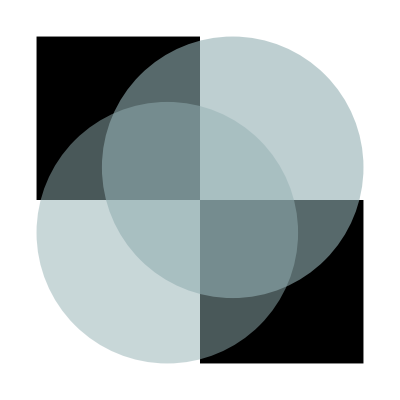
-Graphics--Graphics-

```mathematica
SetUpLCaCbColor["LCaCb",0,"Hue"];Row[{Graphics[{Black,Rectangle[{-1,0.25},{0.25,1.5}],Rectangle[{0.25,-1},{1.5,0.25}],Opacity[0.6],LCaCb[0.7,0.7,0.1],Disk[{0.5,0.5},1],Opacity[0.5],LCaCb[0.7,0.1,0.7],Disk[]}],
Graphics[{Black,Rectangle[{-1,0.25},{0.25,1.5}],Rectangle[{0.25,-1},{1.5,0.25}],LCaCb[0.7,0.7,0.1,0.6],Disk[{0.5,0.5}],LCaCb[0.7,0.1,0.7,0.5],Disk[]}]}]
```

```mathematica
BinPlot3D[bin_,"RGB",tolZero:_:N[1/256],step_:1]:=Module[{r,g,b,rMax,gMax,bMax,minL,maxL,minO,val,vals,LCaCb,LCaCbA,rgb,fBin},
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.03;(* Opacity min*)
{rMax,gMax,bMax}=Dimensions[bin["fBin"]];
Flatten[{EdgeForm[],Table[
vals= Flatten[(bin["fBin"])[[r;;r+step-1,g;;g+step-1,b;;b+step-1]]];
val=Total[vals]/Length[vals];
If[val>tolZero,
{RGBColor[{r/rMax,g/gMax,b/bMax,(1.-minO)  val+minO}],
Cuboid[{r-1,g-1,b-1},{r+step-1,g+step-1,b+step-1}]
}]
,{r,1,rMax,step},{g,1,gMax,step},{b,1,bMax,step}]}]/.Null-> Sequence[]
]
BinPlot3D[bin_,"LCaCb",tolZero:_:N[1/256],step_:1]:=Module[{l,Ca,Cb,lMax,CaMax,CbMax,minL,maxL,minO,val,vals,LCaCb,LCaCbA,rgb,fBin},
SetUpLCaCbColor["LCaCbColor",0];
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.03;(* Opacity min*)
{lMax,CaMax,CbMax}=Dimensions[bin["fBin"]];
Flatten[{EdgeForm[],Table[
vals= Flatten[(bin["fBin"])[[l;;l+step-1,Ca;;Ca+step-1,Cb;;Cb+step-1]]];
val=Total[vals]/Length[vals];
If[val>tolZero,
{LCaCbColor[{l/(lMax) (maxL-minL)+minL,Ca/CaMax,Cb/CbMax,(1.-minO)  val+minO}],
Cuboid[{l-1,Ca-1,Cb-1},{l+step-1,Ca+step-1,Cb+step-1}]
}]
,{l,1,lMax,step},{Ca,1,CaMax,step},{Cb,1,CbMax,step}]}]/.Null-> Sequence[]
]
```

```mathematica
Clear[HistoPlot3D]
Options[HistoPlot3D]={ColorFunction->Function[{Ca,Cb,val},Evaluate[LCaCbColor[0.7,Ca,Cb,val]]]};
HistoPlot3D[bin_,"LCaCb",tolZero:_:N[1/256],drIn_:{},OptionsPattern[] ]:=Module[{l,Ca,Cb,lMax,CaMax,CbMax,minL,maxL,minO,val,vals,LCaCb,LCaCbA,rgb,dr,clrFun},
SetUpLCaCbColor["LCaCbColor",0];
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.3;(* Opacity min*)
{CaMax,CbMax}=Dimensions[bin["fBin"]];
If[Length[drIn]==0,dr={{1,CaMax},{1,CbMax}},dr=drIn];
clrFun=OptionValue[ColorFunction];
Flatten[{EdgeForm[],
Table[val=bin["fBin"][[Ca,Cb]];
If[val>0.001,{EdgeForm[],clrFun[Ca/CaMax,Cb/CbMax,(1.-minO)  val+minO],Cuboid[{Ca-0.5,Cb-0.5,0},{Ca+0.5,Cb+0.5, bin["fBin"][[Ca,Cb]]}]}],{Cb,dr[[2,1]],dr[[2,2]]},{Ca,dr[[1,1]],dr[[1,2]]}]/.Null->Sequence[]
}]
]
```

```mathematica
Clear[BinPlot2D]
BinPlot2D[bin_,"LCaCb",tolZero:_:N[1/256],step_:1]:=Module[{l,Ca,Cb,CaMax,CbMax,minL,maxL,minO,val,vals,LCaCb,LCaCbA,rgb,fBin},
SetUpLCaCbColor["LCaCbColor",0];
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.03;(* Opacity min*)
{CaMax,CbMax}=Dimensions[bin["fBin"]];
l=0.5;
Flatten[{EdgeForm[],Table[
vals= Flatten[(bin["fBin"])[[Ca;;Ca+step-1,Cb;;Cb+step-1]]];
val=Total[vals]/Length[vals];
If[val>tolZero,
{LCaCbColor[{l,Ca/CaMax,Cb/CbMax,(1.-minO)  val+minO}],
Rectangle[{Ca-1,Cb-1},{Ca+step-1,Cb+step-1}]
}]
,{Ca,1,CaMax,step},{Cb,1,CbMax,step}]}]/.Null-> Sequence[]
]
```

```mathematica
Clear[genAnimation]
genAnimation[bin_,{θs_,θe_},{ϕs_,ϕe_},frames_]:=Module[{i,θ,ϕ=Pi/3,stepθ,stepϕ},
stepθ=(θe-θs)/frames;
stepϕ=(ϕe-ϕs)/frames;
Table[
θ=θs+i stepθ;
ϕ=ϕs+i stepϕ;
Rasterize[Graphics3D[bin["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->bin["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> bin["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> bin["PlotLabel"]]],{i,0,frames,1}]
];
```

```mathematica
boundBox[bin_]:={EdgeForm[{Black,Thick}],FaceForm[],Cuboid[{(bin["aMin"]),(bin["aMax"])}]};
skinnedBox[bin_,skinDepth_]:={EdgeForm[{Black,Thick}],FaceForm[],Cuboid[{(bin["aMin"])+skinDepth, (bin["aMax"])-skinDepth}]};
```

```mathematica
topAndTailBox[bin_,depth_]:={EdgeForm[{Black,Thick}],FaceForm[{White,Opacity[0.4]}],Cuboid[{(bin["aMin"]),{(bin["aMin"])[[1]]+depth,(bin["aMax"])[[2]],(bin["aMax"])[[3]]}}],Cuboid[{{(bin["aMax"])[[1]]-depth,(bin["aMin"])[[2]],(bin["aMin"])[[3]]},(bin["aMax"])}]};
```

```mathematica
projectedView[bin_,extra_:{},n_,opts:OptionsPattern[Graphics3D]]:=Module[{viewPoint,axesLabel,axesEdge},
axesEdge={{-1,-1},{-1,-1},{-1,-1}}; axesEdge[[n]]=None;
axesLabel=bin["axisNames"]; axesLabel[[n]]="";
viewPoint={0,0,0}; viewPoint[[n]]=Infinity;
Rasterize[Graphics3D[{bin["PlotData"],extra},Method->{"CuboidPoints"->4},Axes->True,AxesEdge->axesEdge,AxesLabel->axesLabel,ViewPoint->viewPoint,ImageSize->400,Lighting->"Neutral",opts]]]
```

```mathematica
Clear[GaussianFitFun];
GaussianFitFun[x_,y_,μ_,σ_,θ_]:=Module[{xrot,yrot,μrot,ϕ},
(* ϕ=Pi-θ; *)
ϕ=Pi-θ;
xrot=x Cos[ϕ]-y Sin[ϕ];
yrot=x Sin[ϕ]+y Cos[ϕ];
μrot={μ[[1]]*Cos[ϕ]-μ[[2]] Sin[ϕ],μ[[1]] Sin[ϕ]+μ[[2]]*Cos[ϕ]};
Exp[-((xrot-μrot[[1]])^2/(2*σ[[1]]^2)+(yrot-μrot[[2]])^2/(2*σ[[2]]^2))]
]
```

```mathematica
Clear[μσθFromBin];
μσθFromBin[bin_,order_:{1,2}]:=Block[{μ,σ,θ},
μ={bin["gMean"  ][[order[[1]]]],bin["gMean"   ][[order[[2]]]]};
σ={bin["gSigma"][[order[[1]]]],bin["gSigma"][[order[[2]]]]};
If[order=={1,2},θ=bin["gTheta"],θ=Pi-bin["gTheta"]];
{μ,σ,θ}
]
```

```mathematica
Clear[swapMinorMajorAxis];
swapMinorMajorAxis[bin_]:=Block[{μ,σ,θ},
σ={bin["gSigma"][[2]],bin["gSigma"][[1]]};
θ=Mod[bin["gTheta"]+N[Pi/2],2 Pi];
bin["gSigma"]=σ;
bin["gTheta"]=θ;
]
```

```mathematica
Clear[GaussianFit]
GaussianFit[bin_,order_:{1,2}]:=Module[{xx,yy,μ,σ,θ},
{μ,σ,θ} = μσθFromBin[bin,order];
Function[{xx,yy},Evaluate[GaussianFitFun[xx,yy,μ,σ,θ]]]
];
```

```mathematica
Clear[MajorMinorAxesPoints];
MajorMinorAxesPoints[μ_,σ_,θ_,sig_]:={
{{μ[[1]]-sig σ[[1]] Cos[θ],μ[[2]] -sig σ[[1]]Sin[θ] },{μ[[1]]+sig σ[[1]]Cos[θ] ,μ[[2]] +sig σ[[1]] Sin[θ] }},
{{μ[[1]]-sig σ[[2]] Cos[θ-Pi/2],μ[[2]] -sig σ[[2]]Sin[θ-Pi/2] },{μ[[1]]+sig σ[[2]]Cos[θ-Pi/2] ,μ[[2]] +sig σ[[2]] Sin[θ-Pi/2] }}};
```

```mathematica
Clear[dataRange]
If[$VersionNumber>9,
dataRange[bin_,"All",order_:{1,2}]:=Module[{axisTotalA,axisTotalB},
axisTotalA=Total[bin["fBin"],{1}];
axisTotalB=Total[bin["fBin"],{2}];
If[order=={1,2},fun=Sequence,fun=Reverse];
fun[{Flatten[{FirstPosition[axisTotalB,n_ /; n>0],
Length[axisTotalB]-FirstPosition[Reverse[axisTotalB],n_ /; n>0]}],Flatten[{FirstPosition[axisTotalA,n_ /; n>0],
Length[axisTotalA]-FirstPosition[Reverse[axisTotalA],n_ /; n>0]}]}]
],
dataRange[bin_,"All",order_:{1,2}]:=Module[{axisTotalA,axisTotalB},
axisTotalA=Total[bin["fBin"],{1}];
axisTotalB=Total[bin["fBin"],{2}];
If[order=={1,2},fun=Sequence,fun=Reverse];
fun[{Flatten[{First[Position[axisTotalB,n_ /; n>0]],
Length[axisTotalB]-First[Position[Reverse[axisTotalB],n_ /; n>0]]}],Flatten[{First[Position[axisTotalA,n_ /; n>0]],
Length[axisTotalA]-First[Position[Reverse[axisTotalA],n_ /; n>0]]}]}]
]
]
dataRange[bin_,sig_Integer,order_:{1,2}]:=Module[{μ,σ,θ,mmAxes},
{μ,σ,θ} = μσθFromBin[bin,order];
mmAxes=MajorMinorAxesPoints[μ,σ,θ,sig];
{{Min[Flatten[mmAxes[[All,All,1]]]],
Max[Flatten[mmAxes[[All,All,1]]]]},{
Min[Flatten[mmAxes[[All,All,2]]]],
Max[Flatten[mmAxes[[All,All,2]]]]}}
]
```

```mathematica
Clear[elipsePlt];
Protect[EllipsColor];
Options[elipsePlt]={EllipsColor-> Black};
elipsePlt[bin_,sig:_Integer:5,order_:{1,2},opts:OptionsPattern[]]:=elipsePlt[bin,{1,sig},order,opts]
elipsePlt[bin_,sig:_List:{1,5},order_:{1,2},OptionsPattern[]]:=Module[{μ,σ,θ,mmAxes},
{μ,σ,θ} = μσθFromBin[bin,order];
{EdgeForm[{OptionValue[EllipsColor]}],FaceForm[],Table[Rotate[Ellipsoid[μ,i σ],θ],{i,sig[[1]],sig[[2]]}]}
]
```

```mathematica
Clear[fitXPlt];
fitXPlt[bin_,sig_:5,order_:{1,2}]:=Module[{μ,σ,θ,x1,x2,f1,f2,pltRng},
{μ,σ,θ} = μσθFromBin[bin,order];
pltRng = {Min[-(sig+0.2 )σ[[1]],-(sig+0.2 ) σ[[2]]],
               Max[   (sig+0.2 ) σ[[1]],   (sig+0.2 ) σ[[2]]]}+μ[[1]];
Show[Table[
x1=μ[[1]]-i σ[[1]];x2=μ[[1]]+i σ[[1]];
f1=GaussianFitFun[x1,μ[[2]],μ,σ,0];
f2=GaussianFitFun[x2,μ[[2]],μ,σ,0];
{ListPlot[{{x1,f1},{x2,f2}},Frame->True,Axes->False,PlotStyle->Red],Graphics[{Text[i"σ_1",{x1,f1},{1,-1}],Text[Style[ToString[i]<>"σ_1",Small],{x2,f2},{-1,-1}]}]},{i,1,sig}],Plot[GaussianFitFun[x,μ[[2]],μ,σ,0],{x,pltRng[[1]],pltRng[[2]]},AxesLabel->{"Cb'","Frequency"},PlotStyle->Red,PlotRange->{pltRng,{0,1}}],PlotRange->{pltRng,{0,1}},FrameLabel->{{"Frequency",None},{"Cb'","The σ_1 Gaussian"}}]
];
Clear[fitYPlt];
fitYPlt[bin_,sig_:5,order_:{1,2}]:=Module[{μ,σ,θ,y1,y2,f1,f2,pltRng},
{μ,σ,θ} = μσθFromBin[bin,order];
pltRng = {Min[-(sig+0.2 )σ[[1]],-(sig+0.2 ) σ[[2]]],
               Max[   (sig+0.2 ) σ[[1]],   (sig+0.2 ) σ[[2]]]}+μ[[2]];
Show[
 Table[
y1=μ[[2]]-i σ[[2]];y2=μ[[2]]+i σ[[2]];
f1=GaussianFitFun[μ[[1]],y1,μ,σ,0];
f2=GaussianFitFun[μ[[1]],y2,μ,σ,0];
{ListPlot[{{y1,f1},{y2,f2}},Frame->True,Axes->False,PlotStyle->Green],Graphics[{Text[i"σ_2",{y1,f1},{1,-1}],Text[Style[ToString[i]<>"σ_2",Small],{y2,f2},{-1,-1}]}]},{i,1,sig}],Plot[GaussianFitFun[μ[[1]],y,μ,σ,0],{y,pltRng[[1]],pltRng[[2]]},AxesLabel->{"Ca'","Frequency"},PlotStyle->Green,PlotRange->{pltRng,{0,1}}],PlotRange->{pltRng,{0,1}},FrameLabel->{{"Frequency",None},{"Ca'","The σ_2 Gaussian"}}]
];
```

```mathematica
Clear[statTable]
Options[statTable]={Orientation-> "Horizontal"}
statTable[bin_,digits_:3,order_:{1,2},OptionsPattern[]]:=Block[{μ,σ,θ},
{μ,σ,θ} = μσθFromBin[bin,order];
If[OptionValue[Orientation]=="Horizontal",
Grid[{
{"",   Style["θ",Bold],Style["μ",Bold],Style["σ",Bold]},
{"Ca'",NumberForm[θ,digits] ,NumberForm[μ[[1]],digits], NumberForm[σ[[1]], digits]},
{"Cb'",SpanFromAbove        ,NumberForm[μ[[2]],digits], NumberForm[σ[[2]], digits]}
}, Frame->All,Alignment->{Center,Center}],
Grid[{
{ Style["θ",Bold], NumberForm[θ,digits],SpanFromLeft},
{Style["μ",Bold], "Ca", NumberForm[μ[[1]],digits]},
{SpanFromAbove,   "Cb", NumberForm[μ[[2]],digits]},
{Style["σ",Bold], "Ca'", NumberForm[σ[[1]],digits]},
{SpanFromAbove,   "Cb'", NumberForm[σ[[2]],digits]}
}, Frame->All,Alignment->{Center,Center}]
]
]
```

{Orientation→Horizontal}

```mathematica
Clear[fit2DLinesPlt]
Protect[AxisColor,MeanColor,TextColor];
Options[fit2DLinesPlt]={AxisColor-> {Red,Green},TextColor->Black, MeanColor->Blue,PointSize-> 0.25};
fit2DLinesPlt[bin_,sig_:5,order_:{1,2},OptionsPattern[]]:=Module[{sr,μr=1, opcty=0.6},
sr= OptionValue[PointSize];
{μ,σ,θ} = μσθFromBin[bin,order];
Do[mmAxes[i]=MajorMinorAxesPoints[μ,σ,θ,i],{i,1,sig}];
axesPltPnts={Opacity[opcty],OptionValue[MeanColor],Disk[μ,sr],
OptionValue[AxisColor][[1]],Table[{Disk[mmAxes[i][[1,1]],sr],Disk[mmAxes[i][[1,2]],sr]},{i,1,sig}],
OptionValue[AxisColor][[2]], Table[{Disk[mmAxes[i][[2,1]],sr],Disk[mmAxes[i][[2,2]],sr]},{i,1,sig}]};
axesPltLines={Opacity[1],
OptionValue[AxisColor][[1]],Line[mmAxes[sig][[1]]],
OptionValue[AxisColor][[2]], Line[mmAxes[sig][[2]]]};
axesPltTxt={OptionValue[TextColor],
Table[{Text[Style[Subscript[i "σ",Style["1",Small]],Bold,Medium],mmAxes[i][[1,1]],{1,1}],Text[Style[Subscript[i "σ",Style["1",Small]],Bold,Medium],mmAxes[i][[1,2]],{-1,-1}]},{i,1,sig}],
Table[{Text[Style[Subscript[i "σ",Style["2",Small]],Bold,Medium],mmAxes[i][[2,1]],{1,0}],Text[Style[Subscript[i "σ",Style["2",Small]],Bold,Medium],mmAxes[i][[2,2]],{-1,0}]},{i,1,sig}],
Text[Style["μ",Bold],μ+{(-2sr /3) Cos[(Pi/2-θ)],(-2sr /3)  Sin[(Pi/2-θ)]}]};
{axesPltPnts,axesPltLines,axesPltTxt}
]
```

```mathematica
Clear[fit2DAnglePlt];
fit2DAnglePlt[bin_,order_:{1,2}]:=Module[{r=4, opcty=0.6,θs,θe,ϕs,ϕe},
{μ,σ,θ} = μσθFromBin[bin,order];
θs=0; θe = θ;
ϕs=θ; ϕe = Pi/2;
{Graphics[{Opacity[opcty],Green,
Disk[μ,r,{θs,θe}],Opacity[1],Black,Text[Style["θ",Bold,Large],μ+{(2r /3) Cos[(θe+θs)/2],(2r /3)  Sin[(θe+θs)/2]}]}],
Graphics[{Opacity[opcty],Red,
Disk[μ,r,{ϕs,ϕe}],Opacity[1],Black,Text[Style["ϕ",Bold,Large],μ+{(2r /3) Cos[(ϕe+ϕs)/2],(2r /3)  Sin[(ϕe+ϕs)/2]}]}]}
];
```

```mathematica
Clear[fitComparisonPlt]
Options[fitComparisonPlt]={ColorFunction->Function[{Ca,Cb,val},Evaluate[LCaCbColor[0.7,Ca,Cb,val]]],Margin-> 20};
fitComparisonPlt[bin_,order_:{1,2},OptionsPattern[]]:=Module[{CaMax,CbMax,dr,pltRng,boxRto,histoPlt,fun,fitPlt,combPlt3D},
{CaMax,CbMax}=Dimensions[bin["fBin"]];
clrFun=Function[{Ca,Cb,val},Evaluate[OptionValue[ColorFunction][Ca/CaMax,Cb/CbMax,val/1.1]]];
dr=Round[dataRange[bin,"All",order]];
pltRng = {dr[[1]]+{-OptionValue[Margin],OptionValue[Margin]},dr[[2]]+{-OptionValue[Margin],OptionValue[Margin]},{0,1}};
boxRto = Flatten[{N[(dr[[All,2]]-dr[[All,1]])/Max[dr[[All,2]]-dr[[All,1]]]],1}];
histoPlt=Graphics3D[HistoPlot3D[bin,"LCaCb",N[1/1024],dr,ColorFunction-> OptionValue[ColorFunction]],Lighting->"Neutral",Axes->True,AxesLabel->{"Ca","Cb","f"},BoxRatios->boxRto];
fun=GaussianFit[bin,order];
fitPlt=Plot3D[fun[x,y],{x,dr[[1,1]],dr[[1,2]]},{y,dr[[2,1]],dr[[2,2]]},PlotRange-> pltRng,PlotPoints->2 (dr[[1,2]]-dr[[1,1]]),ColorFunction->clrFun,ColorFunctionScaling->False,AxesLabel->{"Ca","Cb","f"},MeshFunctions->{#3&}];
combPlt3D=Show[{fitPlt,histoPlt},
PlotRange->pltRng,
BoxRatios->boxRto];
{{fitPlt,histoPlt}, {PlotRange->pltRng,
BoxRatios->boxRto}}
]
```

```mathematica
Clear[overlayElems]
Options[overlayElems]=Flatten[{AxisSigma->5,EllipsisSigma->{1,5},Options[fit2DLinesPlt],Options[elipsePlt]}];
overlayElems[bin_,order_:{1,2},opts:OptionsPattern[]]:=Module[{axisPlt,elpsPlt,thetaPlt,phiPlt,aspctRatio,dr,combPltOpts},
axisPlt=Graphics[fit2DLinesPlt[bin,OptionValue[AxisSigma],order,FilterRules[{opts},Options[fit2DLinesPlt]]]];
elpsPlt=Graphics[elipsePlt[bin,OptionValue[EllipsisSigma],order,FilterRules[{opts},Options[elipsePlt]]]];
{thetaPlt,phiPlt}=fit2DAnglePlt[bin,order];

dr=dataRange[bin,Max[{OptionValue[EllipsisSigma][[2]],OptionValue[AxisSigma]}]];
aspctRatio=(dr[[2,2]]-dr[[2,1]])/(dr[[1,2]]-dr[[1,1]]);
combPltOpts={PlotRange->dr,AspectRatio->aspctRatio,Frame->True,FrameLabel->{"Ca","Cb"}};
{{axisPlt,elpsPlt,thetaPlt, phiPlt},combPltOpts}
];
```

```mathematica
Clear[gFitElems]
gFitElems[bin_,order_:{1,2}]:=Module[{redPlt,greenPlt,denPlt,denOpacityPlt,axesPlt,elpsPlt,thetaPlt,phiPlt,histoPlt,fitPlt,combPlt3D,combPlt3Dopts,combPlt,combPltOpts,overviewPlt,stat,fun,dr},
dr=dataRange[bin,5];
stat = statTable[bin,4,order];
redPlt    =fitXPlt[bin,5,order];
greenPlt=fitYPlt[bin,5,order];

denPlt=ListDensityPlot[bin["fBin"],AxesLabel->{"Cb","Ca"},InterpolationOrder->0];
denOpacityPlt=Graphics[bin["PlotData"],Frame->True,PlotRange-> bin["PlotRange"],FrameLabel->{{(bin["axisNames"])[[2]],""},{(bin["axisNames"])[[1]],"Overview"}}];

{{axesPlt,elpsPlt,thetaPlt, phiPlt},combPltOpts}=overlayElems[bin,order];
combPlt=Function[{incDen,incAxis,incElps,incTheta,incPhi,incStat},Show[{If[incDen,denOpacityPlt],If[incAxis,axesPlt],If[incElps,elpsPlt],If[incTheta,thetaPlt],If[incPhi,phiPlt]}/.Null->Sequence[],If[incStat,Append[combPltOpts,Epilog-> Inset[stat,Extract[OptionValue[Graphics,combPltOpts,PlotRange],{{1,1},{2,2}}],{Left,Top}]],combPltOpts]]];

{{fitPlt,histoPlt},combPlt3Dopts}=fitComparisonPlt[bin,{1,2},Margin-> 5 ];
combPlt3D=Function[{incFit,incHisto,incStat},Show[{If[incFit,fitPlt],If[incHisto,histoPlt]}/.Null->Sequence[],If[incStat,Append[combPlt3Dopts,Epilog-> Inset[stat,{Left,Top},{Left,Top}]],combPlt3Dopts]]];

overviewPlt=Show[{denOpacityPlt,
Graphics[{FaceForm[],EdgeForm[{Black,Opacity[1]}],Rectangle[{dr[[1,1]],dr[[2,1]]},{dr[[1,2]],dr[[2,2]]}]}]}];
{stat,redPlt,greenPlt,combPlt3D,combPlt,overviewPlt}
];
```

#### Document Generation Routines

```mathematica
Clear[NotebookDefinitionWrite]
SetAttributes[NotebookDefinitionWrite,HoldAllComplete]
NotebookDefinitionWrite[nb_,var_]:=Module[{cell},
cell=Cell[BoxData[RowBox[{var,"=",ToBoxes[Symbol[var]],";"}]],"Input",InitializationCell->True];
NotebookWrite[nb,cell ]]
```

```mathematica
Clear[CellDefinitionWrite]
SetAttributes[CellDefinitionWrite,HoldAllComplete]
CellDefinitionWrite[var_]:=Module[{cell},
cell=Cell[BoxData[RowBox[{var,"=",ToBoxes[Symbol[var]],";"}]],"Input",InitializationCell->True];
CellPrint[cell ]]
```

```mathematica
exportPanelCell[outName_,fileName_]:=Module[{},
Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{
RowBox[{"Panel","[",RowBox[{outName,",",RowBox[{"Background","→","White"}],",",RowBox[{"ImageSize","→","1000"}]}],"]"}],",","\n",
RowBox[{"Button","[",RowBox[{"\"\<Export\>\"",",","\n",RowBox[{
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\""<>fileName<>".jpg\""}],",",outName,",",RowBox[{"ImageResolution","→","300"}]}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\""<>fileName<>".eps\""}],",",outName}],"]"}],";","\n",
RowBox[{"Export","[",RowBox[{RowBox[{"figPath","<>","\""<>fileName<>".pdf\""}],",",outName}],"]"}]}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

```mathematica
BringToFront[list_,n_]:=Module[{tail,head},head=Take[list,n];tail=Drop[list,n];{Sequence@@head,Sequence@@tail}]
```

#### Junk

```mathematica
Clear[AddRGBValuesToBin]
AddRGBValuesToBin[bin_,"RGB",tolZero:_:N[1/256]]:=Module[{r,g,b,rMax,gMax,bMax,minL,maxL,minO,val,LCaCb,LCaCbA,rgb,fBin},
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.3;(* Opacity min*)
{rMax,gMax,bMax}=Dimensions[bin["fBin"]];
Table[
val=(bin["fBin"])[[r,g,b]];
{r/rMax,g/gMax,b/bMax,(1.-minO)  val+minO}
,{r,1,rMax},{g,1,gMax},{b,1,bMax}]
]
AddRGBValuesToBin[bin_,"LCaCb",tolZero:_:N[1/256]]:=Module[{l,Ca,Cb,lMax,CaMax,CbMax,minL,maxL,minO,val,LCaCb,LCaCbA,rgb,fBin},
SetUpLCaCbColor["LCaCbColor",0];
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.3;(* Opacity min*)
{lMax,CaMax,CbMax}=Dimensions[bin["fBin"]];
Table[val=(bin["fBin"])[[l,Ca,Cb]];
col=ColorConvert[LCaCbColor[{l/(lMax) (maxL-minL)+minL,Ca/CaMax,Cb/CbMax,(1.-minO)  val+minO}],"RGB"];
List@@col
,{l,1,lMax},{Ca,1,CaMax},{Cb,1,CbMax}]
]
```

### Set name and path to the matlab stats

```mathematica
TabView[Table[nameSet[[i]]-> Column[{nameSet[[i]],
If[Length[nameSubset[[i]]]>1,
  TabView[ Table[nameSubset[[i,j]]-> Column[{nameSubset[[i,j]],
  If[Length[nameSubSubset[[i,j]]]>1,
     TabView[ Table[nameSubSubset[[i,j,k]]-> Column[{nameSubSubset[[i,j,k]],
     Button["Set",set=ii;subSet=jj;subSubSet=kk; setupFileSystem[ii,jj,kk]]/.{ii->i,jj-> j,kk->k}
     }],{k,1,Length[nameSubSubset[[i,j]]]}]],
     Button["Set",set=ii;subSet=jj;subSubSet=1; setupFileSystem[ii,jj,1]]/.{ii->i,jj-> j}
  ]
  }],{j,1,Length[nameSubset[[i]]]}] ],
   If[Length[nameSubSubset[[i,1]]]>1,
     TabView[ Table[nameSubSubset[[i,1,k]]-> Column[{nameSubSubset[[i,1,k]],
     Button["Set",set=ii;subSet=1;subSubSet=kk; setupFileSystem[ii,1,kk]]/.{ii->i,kk->k}
     }],{k,1,Length[nameSubSubset[[i,1]]]}]],
     Button["Set",set=ii;subSet=1;subSubSet=1; setupFileSystem[ii,1,1]]/.{ii->i}
  ]
]
}],{i,1,Length[nameSet]}]]
```

12345

Set : RGB     Subset :      Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/

3D | 2D
Bin.mat | Bin_Skinned_Rot_TopTail_CaCb.mat
Bin_Skinned.mat | Bin_Skinned_Rot_TopTail_CaCb_Despec.mat
Bin_Skinned_Rot.mat | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat
Bin_Skinned_Rot_TopTail.mat | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
Bin | Bin | Bin_Skinned_Rot_TopTail_CaCb | BinSkinnedRotTopTailCaCb
Bin_Skinned | BinSkinned | Bin_Skinned_Rot_TopTail_CaCb_Despec | BinSkinnedRotTopTailCaCbDespec
Bin_Skinned_Rot | BinSkinnedRot | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | BinSkinnedRotTopTailCaCbDespecblob2
Bin_Skinned_Rot_TopTail | BinSkinnedRotTopTail | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | BinSkinnedRotTopTailCaCbDespecblob1

```mathematica
path=pathBase;
Panel[Row[{Style["Manually Select the directory :",Large],FileNameSetter[Dynamic[path],"Directory"],Dynamic[setupFileSystem[path];path]}]]
```

Manually Select the directory :$CellContext`pathDirectoryAll

Import and Generate Data

```mathematica
title=StringReplace[matLabNames3D[[1]],{"RGB_"->"","_Bin"->""}]
```

Bin

## 1. Fill the Bins

```mathematica
stage=1;
matLabName=matLabNames3D[[stage]]
name=names3D[[stage]]
```

Bin

Bin

### Import and Generate Data

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin

All's Good

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" RGB Bin";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_FSkin_Bin +RGB_FSkin_Index_Pad_Bin +RGB_FSkin_Index_Tip_Bin +RGB_FSkin_Thumb_Pad_Bin +RGB_FSkin_Thumb_Tip_Bin +RGB_JSkin_Bin +RGB_JSkin_Index_Pad_Bin +RGB_JSkin_Index_Tip_Bin +RGB_JSkin_Thumb_Pad_Bin +RGB_JSkin_Thumb_Tip_Bin +RGB_NSkin_Bin +RGB_NSkin_Index_Pad_Bin +RGB_NSkin_Index_Tip_Bin +RGB_NSkin_Thumb_Pad_Bin +RGB_NSkin_Thumb_Tip_Bin |  | 
axisNames | R | G | B
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | 0 |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 255. | 255. | 255.
aScale | 255. | 255. | 255.
count | 7.99027×10^8 |  | 
a | 105.613
141.442
131.388 |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
256
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=4; 
emptyTol = N[1/256];
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Set::setraw: Cannot assign to raw object "Bin RGB Bin".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Bin_Animation/Bin.gif

## 2. Skin the Bins

### Import and Generate Data

```mathematica
stage=2;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin_Skinned

All's Good

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" RGB Bin Skinned";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_FSkin_Bin_Skinned +RGB_FSkin_Index_Pad_Bin_Skinned +RGB_FSkin_Index_Tip_Bin_Skinned +RGB_FSkin_Thumb_Pad_Bin_Skinned +RGB_FSkin_Thumb_Tip_Bin_Skinned +RGB_JSkin_Bin_Skinned +RGB_JSkin_Index_Pad_Bin_Skinned +RGB_JSkin_Index_Tip_Bin_Skinned +RGB_JSkin_Thumb_Pad_Bin_Skinned +RGB_JSkin_Thumb_Tip_Bin_Skinned +RGB_NSkin_Bin_Skinned +RGB_NSkin_Index_Pad_Bin_Skinned +RGB_NSkin_Index_Tip_Bin_Skinned +RGB_NSkin_Thumb_Pad_Bin_Skinned +RGB_NSkin_Thumb_Tip_Bin_Skinned |  | 
axisNames | R | G | B
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | 0 |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 255. | 255. | 255.
aScale | 255. | 255. | 255.
count | 7.47299×10^8 |  | 
a | 99.5536
139.948
129.362 |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
256
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=4; 
emptyTol = N[1/256];
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Set::setraw: Cannot assign to raw object "Bin RGB Bin Skinned".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Bin_Skinned_Animation/Bin_Skinned.gif

## 3. Rotate the Bins

### Import and Generate Data

```mathematica
stage=3;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin_Skinned_Rot

All's Good

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCaCb Bin";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_FSkin_Bin_Skinned_Rot +RGB_FSkin_Index_Pad_Bin_Skinned +RGB_FSkin_Index_Tip_Bin_Skinned +RGB_FSkin_Thumb_Pad_Bin_Skinned +RGB_FSkin_Thumb_Tip_Bin_Skinned +RGB_JSkin_Bin_Skinned_Rot +RGB_JSkin_Index_Pad_Bin_Skinned +RGB_JSkin_Index_Tip_Bin_Skinned +RGB_JSkin_Thumb_Pad_Bin_Skinned +RGB_JSkin_Thumb_Tip_Bin_Skinned +RGB_NSkin_Bin_Skinned_Rot +RGB_NSkin_Index_Pad_Bin_Skinned +RGB_NSkin_Index_Tip_Bin_Skinned +RGB_NSkin_Thumb_Pad_Bin_Skinned +RGB_NSkin_Thumb_Tip_Bin_Skinned |  | 
axisNames | L | Ca | Cb
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | 0 |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 256. | 256. | 256.
aScale | 256. | 256. | 256.
count | 7.47299×10^8 |  | 
a | 122.939
140.252
142.541 |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
257
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
StringFreeQ[name,_~~"Rot"~~___]
```

False

```mathematica
pltCubeScale=4; 
emptyTol = N[1/256];
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Set::setraw: Cannot assign to raw object "Bin LCaCb Bin".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Bin_Skinned_Rot_Animation/Bin_Skinned_Rot.gif

## 4. Top and Tail the Bins

### Import and Generate Data

```mathematica
stage=4;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin_Skinned_Rot_TopTail

All's Good

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCaCb Bin Topped and Tailed";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_FSkin_Bin_Skinned_Rot_TopTail +RGB_FSkin_Index_Pad_Bin_Skinned_Rot_TopTail +RGB_FSkin_Index_Tip_Bin_Skinned_Rot_TopTail +RGB_FSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail +RGB_FSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail +RGB_JSkin_Bin_Skinned_Rot_TopTail +RGB_JSkin_Index_Pad_Bin_Skinned_Rot_TopTail +RGB_JSkin_Index_Tip_Bin_Skinned_Rot_TopTail +RGB_JSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail +RGB_JSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail +RGB_NSkin_Bin_Skinned_Rot_TopTail +RGB_NSkin_Index_Pad_Bin_Skinned_Rot_TopTail +RGB_NSkin_Index_Tip_Bin_Skinned_Rot_TopTail +RGB_NSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail +RGB_NSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail |  | 
axisNames | L | Ca | Cb
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | 0 |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 256. | 256. | 256.
aScale | 256. | 256. | 256.
count | 6.97383×10^8 |  | 
a | 127.7
140.626
143.012 |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
257
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=4; 
emptyTol = N[1/256];
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Set::setraw: Cannot assign to raw object "Bin LCaCb Bin Topped and Tailed".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Bin_Skinned_Rot_TopTail_Animation/Bin_Skinned_Rot_TopTail.gif

## 5. Collapse the Bins

### Import and Generate Data

```mathematica
stage=5;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

Bin_Skinned_Rot_TopTail_CaCb

BinSkinnedRotTopTailCaCb

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin_Skinned_Rot_TopTail_CaCb

All's Good

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"Ca","Cb"};
Symbol[name]["PlotLabel"] = title<>" CaCb Bin";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb +RGB_FSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_FSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_FSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_FSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb +RGB_JSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_JSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_JSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_JSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb +RGB_NSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_NSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_NSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_NSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 0. | 0.
gSigma | 0. | 0.
gTheta | 0. | 
gAmp | 1. | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 6.97383×10^8 | 
a | 140.626
143.012 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=1; 
emptyTol = N[1/256];
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[name],"LCaCb",emptyTol,pltCubeScale];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Set::setraw: Cannot assign to raw object "Bin CaCb Bin".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

## 6. Despeckle the Bins

### Import and Generate Data

```mathematica
stage=6;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

Bin_Skinned_Rot_TopTail_CaCb_Despec

BinSkinnedRotTopTailCaCbDespec

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : Bin_Skinned_Rot_TopTail_CaCb_Despec

All's Good

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"Ca","Cb"};
Symbol[name]["PlotLabel"] = title<>" CaCb Bin Despeckled";
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec +RGB_FSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_FSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_FSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_FSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec +RGB_JSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_JSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_JSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_JSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec +RGB_NSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_NSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc +RGB_NSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc +RGB_NSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 0. | 0.
gSigma | 0. | 0.
gTheta | 0. | 
gAmp | 1. | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 6.97383×10^8 | 
a | 140.626
143.012 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=1; 
emptyTol = N[1/1024];
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[name],"LCaCb",emptyTol,pltCubeScale];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Set::setraw: Cannot assign to raw object "Bin CaCb Bin Despeckled".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

## 7. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2D[[stage-4;;]]
names=names2D[[stage-4;;]]
```

{Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2,Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1}

{BinSkinnedRotTopTailCaCbDespecblob2,BinSkinnedRotTopTailCaCbDespecblob1}

### Import and Generate Data

#### Import Data

```mathematica
Do[
Print["Loading : "<>matLabNames[[i]]];
ImportMatlabData[names[[i]],matLabNames[[i]],path],
{i,1,Length[names]}]
```

Loading : Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2

All's Good

Loading : Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1

All's Good

Correct Axes names

```mathematica
Do[Symbol[names[[i]]]["axisNames"]={"Ca","Cb"},
{i,1,Length[names]}];
Do[
Symbol[names2D[[i]]]["PlotLabel"] = title<>" CaCb Bin Blob"<>ToString[i-2];,
{i,3,Length[names2D]}];
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Do[Print["Saving : "<> names[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames[[i]]<>".m"];
Save[path<>"Data"<>"/"<>matLabNames[[i]]<>".m",Evaluate[names[[i]]]],
{i,1,Length[names]}];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/" already exists.

Saving : BinSkinnedRotTopTailCaCbDespecblob2 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.m

Saving : BinSkinnedRotTopTailCaCbDespecblob1 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.m

Check the import

```mathematica
Do[Print[Row[{TableForm[Map[(Symbol[names[[i]]][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[names[[i]]][#]]})&,fields[[5;;8]]]]}]],
{i,1,Length[names]}]
```

name | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 +RGB_FSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_FSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_FSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_FSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 +RGB_JSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_JSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_JSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_JSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 +RGB_NSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_NSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_NSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob2 +RGB_NSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob2 | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 108.537 | 86.8571
gSigma | 6.25635 | 2.69955
gTheta | 0.931157 | 
gAmp | 0.9 | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 2.12091×10^8 | 
a | 118.588
104.268 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

name | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 +RGB_FSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_FSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_FSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_FSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 +RGB_JSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_JSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_JSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_JSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 +RGB_NSkin_Index_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_NSkin_Index_Tip_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_NSkin_Thumb_Pad_Bin_Skinned_Rot_TopTail_bc blob1 +RGB_NSkin_Thumb_Tip_Bin_Skinned_Rot_TopTail_bc blob1 | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | 0 | 
gMean | 164.663 | 181.397
gSigma | 10.7802 | 0.957193
gTheta | 1.00761 | 
gAmp | 0.9 | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 3.83248×10^8 | 
a | 153.532
164.946 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
Do[
pltCubeScale=1; 
emptyTol = N[1/1024];
Evaluate[ToExpression[names[[i]]<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[names[[i]]],"LCaCb",emptyTol,pltCubeScale];
Evaluate[ToExpression[names[[i]]<>"[\"PlotRange\"]"]] = Transpose[{Symbol[names[[i]]]["aMin"],Symbol[names[[i]]]["aMax"]}];
Evaluate[ToExpression[names[[i]]<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[names[[i]]]["name"],"_"-> " "];
If[Length[ToExpression[names[[i]]<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]];
If[Length[ToExpression[names[[i]]<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]],
{i,1,Length[names]}]
```

Set::setraw: Cannot assign to raw object "Bin CaCb Bin Blob1".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Set::setraw: Cannot assign to raw object "Bin CaCb Bin Blob2".

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Do[Print["Saving : "<> names[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames[[i]]<>".m"];
Save[path<>"Data"<>"/"<>matLabNames[[i]]<>".m",Evaluate[names[[i]]]],
{i,1,Length[names]}];
```

Saving : BinSkinnedRotTopTailCaCbDespecblob2 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.m

Saving : BinSkinnedRotTopTailCaCbDespecblob1 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/Data/Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.m

Generate the Plot Notebook

## 0. Init

```mathematica
title=StringReplace[matLabNames3D[[1]],{"RGB_"->"","_Bin"->""}];
```

```mathematica
outputNotebook=path<>matLabNames3D[[1]]<>"_plots.nb"
nb=CreateDocument[];
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/JSkin/comb/mathematica/RGB_JSkin_Bin_plots.nb

```mathematica
outNames = {"Fill","Skin","Rotate","TopnTail","Collapse","Despeckle","Blobs","Fit","Export"};
figNames = {"Fill_the_Bins","Skin_the_Bins","Rotate_the_Bins","Top_and_Tail_the_Bins","Collapse_the_Bins","Despeckle_the_Bins","Find_the_Blobs","Fit_the_Gaussian","Export"};
figPath = path<>"Figs/";
CreateDirectory[figPath];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/JSkin/comb/mathematica/Figs/" already exists.

```mathematica
NotebookWrite[nb,Cell[title,"Chapter"]]
```

```mathematica
NotebookWrite[nb,Cell["Init","Section"]]
NotebookDefinitionWrite[nb,"path"]
NotebookDefinitionWrite[nb,"figPath"]
NotebookDefinitionWrite[nb,"figNames"]
NotebookDefinitionWrite[nb,"filenames2D"]
NotebookDefinitionWrite[nb,"matLabNames2D"]
NotebookDefinitionWrite[nb,"names2D"]
NotebookDefinitionWrite[nb,"filenames3D"]
NotebookDefinitionWrite[nb,"matLabNames3D"]
NotebookDefinitionWrite[nb,"names3D"]
(* 
Possibly add function definitions to the oputput.

Map[NotebookDefinitionWrite[nb,#]&,{"LCaCbColorFast","SetUpLCaCbColor","HistoPlot3D","boundBox","skinnedBox","topAndTailBox","projectedView","GaussianFitFun","μσθFromBin","GaussianFit","MajorMinorAxesPoints","dataRange","elipsePlt","fitXPlt","fitYPlt","statTable","fit2DLinesPlt","fit2DAnglePlt","fitComparisonPlt","overlayElems","gFitElems"}]
*)
```

```mathematica
NotebookSave[nb,outputNotebook]
```

## 1. Fill the Bins

```mathematica
stage=1;
matLabName=matLabNames3D[[stage]]
name=names3D[[stage]]
```

RGB_JSkin_Bin

RGBJSkinBin

### Generate the Plot Notebook

```mathematica
stage=1;
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" RGB Bin";
```

```mathematica
Symbol[names3D[[stage]]]["PlotLabel"]
```

JSkin RGB Bin

```mathematica
stage=1;
NotebookWrite[nb,Cell["1. Fill the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[1]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m"<>"\"",",","\""<>names3D[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

```mathematica
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"SaveDefinitions","→","True"}]}],"]"}],"
"}]],"Code"]]
```

```mathematica
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"θ","=",RowBox[{"5",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"5",RowBox[{"Pi","/","12"}]}]}],",","isoView",",","redView",",","greenView",",","blueView",",",RowBox[{"skinDepth","=","9"}]}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView"  ,"=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView" ,"=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

## 2. Skin the Bins

```mathematica
stage=2;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" RGB Bin Skinned";
```

### Generate the Plot Notebook

```mathematica
stage=2;
NotebookWrite[nb,Cell["2. Skin the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[2]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m"<>"\"",",","\""<>names3D[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"θ","=",RowBox[{"5",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"5",RowBox[{"Pi","/","12"}]}]}],",","isoView",",","redView",",","greenView",",","blueView",",",RowBox[{"skinDepth","=","9"}]}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

## 3. Rotate the Bins

```mathematica
stage=3;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCaCb Bin";
```

### Generate the Plot Notebook

```mathematica
stage=3;
NotebookWrite[nb,Cell["3. Rotate the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[3]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m"<>"\"",",","\""<>names3D[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

```mathematica
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

```mathematica
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"SaveDefinitions","→","True"}]}],"]"}],"
"}]],"Code"]]
```

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"depth","=",depth}],",",RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView"}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}],",",RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",",","0"}],"}"}]}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{"boundBox","[",names3D[[stage]],"]"}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

## 4. Top and Tail the Bins

```mathematica
stage=4;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
Symbol[names3D[[stage]]]["PlotLabel"] = title<>" LCaCb Bin Topped and Tailed";
```

### Generate the Plot Notebook

```mathematica
stage=4;
depth=42;
NotebookWrite[nb,Cell["4. Top and Tail the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[4]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" LCaCb Bin Topped and Tailed"<>"\""}]}]],"Input"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m"<>"\"",",","\""<>names3D[[stage]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Code"]]
```

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"depth","=",depth}],",",RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView"}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}],",",RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",",","0"}],"}"}]}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{"boundBox","[",names3D[[stage]],"]"}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

## 5. Collapse the Bins

```mathematica
stage=5;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
Symbol[names2D[[stage-4]]]["PlotLabel"] = title<>" CaCb Bin";
```

RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb

RGBJSkinBinSkinnedRotTopTailCaCb

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["5. Collapse the Bins","Section"]]
```

```mathematica
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[1]]<>".m")],"]",";"}]],"Code"] ]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin"<>"\""}]}]],"Input"]
]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[stage-4]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[stage-4]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2D[[stage-4]]<>".m"<>"\"",",","\""<>names2D[[stage-4]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

```mathematica
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[
RowBox[{"GraphicsRow","[",RowBox[{"{",RowBox[{RowBox[{"ListDensityPlot","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2D[[1]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"FrameLabel","→",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"InterpolationOrder","→","0"}]}],"]"}],",",
RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],"}"}],"]"}]],"Code"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",
RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

## 6. Despeckle the Bins

```mathematica
stage=6;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
Symbol[names2D[[stage-4]]]["PlotLabel"] = title<>" CaCb Bin Despeckled";
```

RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec

RGBJSkinBinSkinnedRotTopTailCaCbDespec

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["6. Despeckle the Bins","Section"]]
```

```mathematica
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")],"]",";"}]],"Code"] ],
{i,1,Length[names2D]}]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin Despeckled"<>"\""}]}]],"Input"]
]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[stage-4]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[stage-4]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[stage-4]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2D[[stage-4]]<>".m"<>"\"",",","\""<>names2D[[stage-4]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
]
```

```mathematica
NotebookWrite[nb,Cell["Despeckle Plot","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","dr",",","windows",",","blobPlt",",","blobsPlt",",","blobsDespecPlt"}],"}"}],",","
",RowBox[{RowBox[{"dr","=",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","\n",RowBox[{"windows","=",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(",RowBox[{"dr","[",RowBox[{"[","i","]"}],"]"}],")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"ToString","[","i","]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{"i",",","1",",",RowBox[{"Length","[","dr","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}]}],";","
","\n",RowBox[{"blobPlt"," ","="," ",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{"windows",",","\n",RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
","\n",RowBox[{"blobsPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"blobsDespecPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}],"<>","\"\< Despeckled\>\""}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize"," → ","1000"}]}],"]"}]}]}],"\n","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

```mathematica
NotebookWrite[nb,Cell["Surface plots","Subsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{"dr",",","hist"}],"}"}],",","\n",RowBox[{RowBox[{"dr","=",RowBox[{"Round","[",RowBox[{"dataRange","[",RowBox[{names2D[[2]],",","\"\<All\>\""}],"]"}],"]"}]}],";","
",RowBox[{title<>"outCollapse","=",RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"\"\<\>\"",",",RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",","\"\<Overview\>\""}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","200"}]}],"]"}]}],";","
",RowBox[{"hist","=",RowBox[{"HistoPlot3D","[",RowBox[{names2D[[2]],",","\"\<LCaCb\>\"",",",RowBox[{"N","[",RowBox[{"1","/","1024"}],"]"}],",","dr"}],"]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]]<>"HistoPlt","=",RowBox[{"Graphics3D","[",RowBox[{"hist",",",RowBox[{"Lighting","→","\"\<Neutral\>\""}],",",RowBox[{"Axes","->","True"}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",",RowBox[{"Column","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Frequency\>\"",",","Bold"}],"]"}],",","\"\<f\>\""}],"}"}],",",RowBox[{"Alignment","→","Center"}]}],"]"}]}],"}"}]}],",",RowBox[{"BoxRatios","→",RowBox[{"{",RowBox[{"1",",","1",",","1"}],"}"}]}],",",RowBox[{"ImageSize","→","600"}]}],"]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]]<>"SurfHistPlt","=",RowBox[{"ListPlot3D","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2D[[2]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"ColorFunction","→",RowBox[{"Function","[",RowBox[{RowBox[{"{",RowBox[{"x",",","y",",","z"}],"}"}],",",RowBox[{"LCaCbColor","[",RowBox[{"{",RowBox[{"0.5",",","x",",","y"}],"}"}],"]"}]}],"]"}]}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"PlotRange","→","dr"}]}],"]"}]}],";","\n",
RowBox[{title<>"outDespeckleHistoOverviewPlt","=",RowBox[{"Grid","[",RowBox[{RowBox[{"{",RowBox[{"{",RowBox[{title<>"out"<>outNames[[stage]]<>"HistoPlt",",",title<>"outCollapse"}],"}"}],"}"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{"Left",",","Top"}],"}"}]}],",",RowBox[{"Spacings","→","0"}]}],"]"}]}]}]}],"\n","
","]"}],";"}],"\n",
RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{
exportPanelCell[title<>"out"<>outNames[[stage]]<>"HistoOverviewPlt",figNames[[stage]]<>"_Surf"]
,",","\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>"HistoPlt",figNames[[stage]]<>"_Surf"]
,",","\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>"SurfHistPlt",figNames[[stage]]<>"_Surf"]
}],"}"}],"]"}]
}],"Code"]
]
```

## 7. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2D[[stage-4;;]];
names=names2D[[stage-4;;]];
Do[
Symbol[names2D[[i]]]["PlotLabel"] = title<>" CaCb Bin Blob"<>ToString[i-2];,
{i,3,Length[names2D]}];
```

```mathematica
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2D[[i]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin Blob"<>ToString[i-2]<>"\""}]}]],"Input"]
],
{i,3,Length[names2D]}];
```

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["7. Find the Blobs","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{names2D[[i]],"[","\"\<PlotLabel\>\"","]"}]," ","="," ",RowBox[{"\""<>title<>" CaCb Bin Blob"<>ToString[i-2]<>"\""}]}]],"Input"]
], {i,3,Length[names2D]}];
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")],"]",";"}]],"Code"] ];
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Name\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[i]],"[","\"\<name\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[i]],"[","\"\<name\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Style","[",RowBox[{"\"\<PlotLabel\>\"",",","20"}],"]"}],",","
",RowBox[{"InputField","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{names2D[[i]],"[","\"\<PlotLabel\>\"","]"}],"]"}],",","String",",",RowBox[{"FieldSize","→",RowBox[{"StringLength","[",RowBox[{names2D[[i]],"[","\"\<PlotLabel\>\"","]"}],"]"}]}]}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"<>"\"",",","\""<>names2D[[i]]<>"\""}],"]"}]}],"]"}]}],"}"}],"]"}],"]"}]],"Code"]
],
{i,3,Length[names2D]}];
```

```mathematica
NotebookWrite[nb,Cell["Blob Plot","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","blobPlt",",","blobsPlt"}],"}"}],",","
",RowBox[{RowBox[{"order","=",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],";",RowBox[{"blobPlt","=",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","[",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}]}],";",RowBox[{"{",RowBox[{RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",",RowBox[{"{","2",",","2","}"}],",","order"}],"]"}],",",RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(","dr",")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}],",",RowBox[{names2D[[2]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[2]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[2]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
",RowBox[{"blobsPlt","=",RowBox[{"Table","[","
",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}]}],";","
",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",",RowBox[{"{","2",",","2","}"}],",","order"}],"]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ","dr"}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}]}],"}"}]}],"}"}]}]}],"]"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}]}],"]"}]}]}],"
","]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]],figNames[[stage]]]
}],"Code"]
]
```

## 8. Fit the Gaussian

```mathematica
stage=8;
blob=0;
name=names2D[[3+blob]]
```

RGBJSkinBinSkinnedRotTopTailCaCbDespecblob2

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["8. Fit the Gaussian","Section"]]
```

```mathematica
Do[
NotebookWrite[nb,Cell["Blob : "<>ToString[blob],"Subsection"]];
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"SetUpLCaCbColor","[","0","]"}],";"}]],"Code"]];
NotebookWrite[nb,Cell[BoxData[RowBox[ { RowBox[{RowBox[{"{",RowBox[{"stat"<>ToString[blob],",","redPlt"<>ToString[blob],",","greenPlt"<>ToString[blob],",","combPlt3DFun"<>ToString[blob],",","combPltFun"<>ToString[blob],",","overviewPlt"<>ToString[blob]}],"}"}],"=",RowBox[{"gFitElems","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],"]"}]}],";"}]],"Code"]
];
NotebookWrite[nb,Cell[BoxData[RowBox[{"Panel","[",RowBox[{RowBox[{"Grid","[",RowBox[{RowBox[{"{",RowBox[{"{",RowBox[{RowBox[{"DynamicModule","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"incFit","=","True"}],",",RowBox[{"incHisto","=","True"}],",",RowBox[{"incStat","=","False"}]}],"}"}],",","
",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"Framed","[",RowBox[{"Panel","[",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<Fit\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incFit","]"}],"]"}],",","
","\"\<  Histo\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incHisto","]"}],"]"}],",","
","\"\<  Stat\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incStat","]"}],"]"}]}],"}"}],"]"}],"]"}],"]"}],",","
",RowBox[{"Panel","[",RowBox[{"Dynamic","[",RowBox[{RowBox[{RowBox[{"combPlt3D"<>ToString[blob],"=",RowBox[{"combPlt3DFun"<>ToString[blob],"[",RowBox[{"incFit",",","incHisto",",","incStat"}],"]"}]}],";",RowBox[{"Show","[",RowBox[{"combPlt3D"<>ToString[blob],",",RowBox[{"ImageSize","→","500"}]}],"]"}]}],",",RowBox[{"Background","→","White"}]}],"]"}],"
","]"}]}],"}"}],",",RowBox[{"Alignment","→","Center"}]}],"]"}],"]"}]}],"
","]"}],",","
",RowBox[{"DynamicModule","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"incDen","=","True"}],",",RowBox[{"incAxis","=","True"}],",",RowBox[{"incElps","=","True"}],",",RowBox[{"incTheta","=","True"}],",",RowBox[{"incPhi","=","False"}],",",RowBox[{"incStat","=","True"}]}],"}"}],",","
",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"Framed","[",RowBox[{"Panel","[",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<Density\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incDen","]"}],"]"}],",","
","\"\<  Axis\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incAxis","]"}],"]"}],",","
","\"\<  Elipsis\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incElps","]"}],"]"}],",","\"\<  θ\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incTheta","]"}],"]"}],",","\"\<  ϕ\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incPhi","]"}],"]"}],",","\"\<  Stat\>\"",",",RowBox[{"Checkbox","[",RowBox[{"Dynamic","[","incStat","]"}],"]"}]}],"}"}],"]"}],"]"}],"]"}],",","
",RowBox[{"Panel","[",RowBox[{RowBox[{"Dynamic","[",RowBox[{RowBox[{"combPlt"<>ToString[blob],"=",RowBox[{"combPltFun"<>ToString[blob],"[",RowBox[{"incDen",",","incAxis",",","incElps",",","incTheta",",","incPhi",",","incStat"}],"]"}]}],";",RowBox[{"Show","[",RowBox[{"combPlt"<>ToString[blob],",",RowBox[{"ImageSize","→","500"}]}],"]"}]}],"]"}],",",RowBox[{"Background","→","White"}]}],"]"}]}],"
","}"}],",",RowBox[{"Alignment","→","Center"}]}],"]"}],"]"}]}],"
","]"}]}],"
","}"}],"}"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{"Left",",","Top"}],"}"}]}]}],"]"}],",",RowBox[{"Style","[",RowBox[{"\"\<Choose the elements to display\>\"",",","20"}],"]"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{"Left",",","Top"}],"}"}]}]}],"]"}]],"Code"]
];

NotebookWrite[nb,Cell[BoxData[RowBox[{"
",RowBox[{"TabView","[",RowBox[{"{",RowBox[{RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab1","=",RowBox[{"Grid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<PlotLabel\>\"","]"}],",","Large",",","Bold"}],"]"}],",","stat1"}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","overviewPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","redPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"ImageSize","→","1000"}]}],"]"}],",","SpanFromLeft"}],"}"}]}],"}"}],","," ",RowBox[{"Frame","→","True"}],",",RowBox[{"Alignment","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"Left",",","Right"}],"}"}],",","Center"}],"}"}]}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab1",figNames[[8]]<>ToString[blob]]
}]],",","
",Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab2","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","              ","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt"<>ToString[blob],",","     ","SpanFromLeft",",","   ","redPlt"<>ToString[blob],",","                ","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab2",figNames[[8]]<>ToString[blob]]
}]]}],"}"}],"]"}],",","
",RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab3","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","overviewPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","redPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab3",figNames[[8]]<>ToString[blob]]
}]],",","
",Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab4","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D"<>ToString[blob],",","         ","SpanFromLeft",",","combPlt"<>ToString[blob],",","              ","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt"<>ToString[blob],",","     ","SpanFromLeft",",","redPlt"<>ToString[blob],",","               ","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab4",figNames[[8]]<>ToString[blob]]
}]]}],"}"}],"]"}],",","
",RowBox[{"TabView","[",RowBox[{"{","
",RowBox[{Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab5","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","overviewPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","redPlt"<>ToString[blob]}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab5",figNames[[8]]<>ToString[blob]]
}]],",","
",Sequence[RowBox[{RowBox[{RowBox[{title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab6","=",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt"<>ToString[blob],",","             ","SpanFromLeft",",","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt"<>ToString[blob],",","    ","redPlt"<>ToString[blob],",","              ","greenPlt"<>ToString[blob]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}],",",RowBox[{"ImageSize","→","1000"}],",",RowBox[{"Background","->","White"}]}],"]"}]
}],";"}],"\n",
exportPanelCell[title<>"out"<>outNames[[stage]]<>ToString[blob]<>"Tab6",figNames[[8]]<>ToString[blob]]
}]]}],"}"}],"]"}]}],"
","}"}],"]"}]}]],"Code"]

];

,{blob,0,Length[names2D]-3}]
```

## 9. Combine the Plots Output

```mathematica
stage=9;
blob=0;
name=names2D[[3+blob]]
```

RGBJSkinBinSkinnedRotTopTailCaCbDespecblob2

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["9. Combine the Plots Output","Section"]]
```

```mathematica
NotebookWrite[nb,Cell["Re-evaluate to generate new colors or choose one!","Text"]]
```

```mathematica
NotebookWrite[nb,
Cell[BoxData[RowBox[{"If","[",RowBox[{RowBox[{"TrueQ","[",RowBox[{RowBox[{"Head","[",RowBox[{names2D[[3+blob]],"[","\"\<fitPlotColor\>\"","]"}],"]"}],"==","Directive"}],"]"}],",",RowBox[{"initColor","=",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<fitPlotColor\>\"","]"}],"[",RowBox[{"[","2","]"}],"]"}]}],",",RowBox[{"initColor","=",RowBox[{"RGBColor","[",RowBox[{RowBox[{"RandomReal","[","]"}],",",RowBox[{"RandomReal","[","]"}],",",RowBox[{"RandomReal","[","]"}]}],"]"}]}]}],"]"}]],"Code"]
];
```

```mathematica
NotebookWrite[nb,Cell[BoxData[{RowBox[{"Panel","[",RowBox[{"DynamicModule","[",RowBox[{RowBox[{"{",
RowBox[{RowBox[{"color","=","initColor"}],",",
RowBox[{"opcty","=","1"}],",",
RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Graphics3D","[",RowBox[{"{",RowBox[{"Cuboid","[",RowBox[{RowBox[{"{",RowBox[{"0",",","0",",","0"}],"}"}],",",RowBox[{"{",RowBox[{"255",",","255",",","255"}],"}"}]}],"]"}],"}"}],"]"}]}],",",
RowBox[{"AxisLineThickness","=","4.0"}],",",RowBox[{"EllipsLineThickness","=","4.0"}],",",
RowBox[{"sig","=",RowBox[{"{",RowBox[{"2",",","4"}],"}"}]}],",",RowBox[{"len","=","10"}],",",RowBox[{"endSig","=","5"}],",",
RowBox[{"txtColor","=","initColor"}],",",RowBox[{"txtOpacity","=","0"}],",",RowBox[{"ellipsColor","=","initColor"}],",",
RowBox[{"ellipsOpacity","=","0.8"}],",",RowBox[{"axisColor","=","initColor"}],",",RowBox[{"axisOpacity","=","0.8"}],",",
RowBox[{"out2D","=",RowBox[{"Graphics","[",RowBox[{"{",RowBox[{"Rectangle","[",RowBox[{RowBox[{"{",RowBox[{"0",",","0"}],"}"}],",",RowBox[{"{",RowBox[{"255",",","255"}],"}"}]}],"]"}],"}"}],"]"}]}]}],"}"}],",","
",RowBox[{"Column","[",RowBox[{"{","
",RowBox[{RowBox[{"Row","[",RowBox[{"{",RowBox[{RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{","
",RowBox[{RowBox[{RowBox[{"Grid","[",RowBox[{"{",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Axis\>\"",",","Bold"}],"]"}],",",RowBox[{"ColorSetter","[",RowBox[{"Dynamic","[","color","]"}],"]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","opcty","]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"]"}]}],"}"}],"}"}],"]"}],"
",RowBox[{"Button","[",RowBox[{"\"\<Generate\>\"",",",RowBox[{RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<fitPlot\>\"","]"}],"=."}],";","
",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<fitPlotColor\>\"","]"}],"=."}],";","
",RowBox[{RowBox[{"Evaluate","[",RowBox[{names2D[[3+blob]],"[","\"\<fitPlotColor\>\"","]"}],"]"}]," ","="," ",RowBox[{"Directive","[",RowBox[{RowBox[{"Opacity","[","opcty","]"}],",","color"}],"]"}]}],";","
",RowBox[{"axisColor","="," ","color"}],";",RowBox[{"ellipsColor","="," ","color"}],";",RowBox[{"txtColor","=","color"}],";","
",RowBox[{RowBox[{"Evaluate","[",RowBox[{names2D[[3+blob]],"[","\"\<fitPlot\>\"","]"}],"]"}],"=",RowBox[{"fitComparisonPlt","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}],",",RowBox[{"Margin","→"," ","5"}],",",RowBox[{"ColorFunction","→",RowBox[{"Function","[",RowBox[{RowBox[{"{",RowBox[{"Ca",",","Cb",",","val"}],"}"}],",",RowBox[{"Directive","[",RowBox[{"{",RowBox[{RowBox[{"Opacity","[",RowBox[{"val","/","1.1"}],"]"}],",","color"}],"}"}],"]"}]}],"]"}]}]}]," ","]"}]}],";","
",RowBox[{title<>"out"<>outNames[[stage]],"=",RowBox[{"Show","[",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<fitPlot\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<fitPlot\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}]}],"]"}]}]}]}],"
","]"}]}],",","
",RowBox[{"Panel","[",RowBox[{RowBox[{"Dynamic","[",title<>"out"<>outNames[[stage]],"]"}],",",RowBox[{"Background","→","White"}]}],"]"}]}],"
","}"}],"]"}],"]"}],",","
",RowBox[{"Panel","[",RowBox[{"Column","[",RowBox[{"{","
",RowBox[{RowBox[{"Grid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Axis\>\"",",","Bold"}],"]"}],",",RowBox[{"ColorSetter","[",RowBox[{"Dynamic","[","axisColor","]"}],"]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","axisOpacity","]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Ellips\>\"",",","Bold"}],"]"}],",",RowBox[{"ColorSetter","[",RowBox[{"Dynamic","[","ellipsColor","]"}],"]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","ellipsOpacity","]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Text\>\"",",","Bold"}],"]"}],",",RowBox[{"ColorSetter","[",RowBox[{"Dynamic","[","txtColor","]"}],"]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","txtOpacity","]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Sig\>\"",",","Bold"}],"]"}],",",RowBox[{"Dynamic","[","sig","]"}],",",RowBox[{"IntervalSlider","[",RowBox[{RowBox[{"Dynamic","[","sig","]"}],",",RowBox[{"{",RowBox[{"1",",","10",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<len\>\"",",","Bold"}],"]"}],",",RowBox[{"Dynamic","[","len","]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","len","]"}],",",RowBox[{"{",RowBox[{"1",",","10",",","1"}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Ellipse Thick\>\"",",","Bold"}],"]"}],",",RowBox[{"Dynamic","[","EllipsLineThickness","]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","EllipsLineThickness","]"}],",",RowBox[{"{",RowBox[{"0",",","25"}],"}"}]}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"Style","[",RowBox[{"\"\<Axis Thick\>\"",",","Bold"}],"]"}],",",RowBox[{"Dynamic","[","AxisLineThickness","]"}],",",RowBox[{"Slider","[",RowBox[{RowBox[{"Dynamic","[","AxisLineThickness","]"}],",",RowBox[{"{",RowBox[{"0",",","25"}],"}"}]}],"]"}]}],"}"}]}],"}"}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Generate\>\"",",",RowBox[{RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<overlayElems\>\"","]"}],"=."}],";","
",RowBox[{RowBox[{"Evaluate","[",RowBox[{names2D[[3+blob]],"[","\"\<overlayElems\>\"","]"}],"]"}],"=",RowBox[{"overlayElems","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}],",",
RowBox[{"AxisColor","→"," ",RowBox[{"{",RowBox[{RowBox[{"Directive","[",RowBox[{RowBox[{"AbsoluteThickness","[","AxisLineThickness","]"}],",",RowBox[{"Opacity","[","axisOpacity","]"}],",","axisColor"}],"]"}],",",RowBox[{"Directive","[",RowBox[{RowBox[{"Opacity","[","axisOpacity","]"}],",","axisColor"}],"]"}]}],"}"}]}],","," ",
RowBox[{"TextColor","→",RowBox[{"Directive","[",RowBox[{RowBox[{"Opacity","[","txtOpacity","]"}],",","txtColor"}],"]"}]}],",",
RowBox[{"MeanColor","→","Blue"}],",",RowBox[{"PointSize","→"," ","0.5"}],",",
RowBox[{"EllipsColor","→"," ",RowBox[{"Directive","[",RowBox[{RowBox[{"AbsoluteThickness","[","EllipsLineThickness","]"}],",",RowBox[{"Opacity","[","ellipsOpacity","]"}],",","ellipsColor"}],"]"}]}],",",
RowBox[{"EllipsisSigma","→","sig"}],",",
RowBox[{"AxisSigma","→","len"}]}],"]"}]}],";","
",RowBox[{"out2D","=",RowBox[{"Show","[",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<overlayElems\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<overlayElems\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}]}],"]"}]}]}]}],"
","]"}],",","
",RowBox[{"Panel","[",RowBox[{RowBox[{"Dynamic","[","out2D","]"}],",",RowBox[{"Background","→","White"}]}],"]"}]}],"
","}"}],"]"}],"]"}]}],"}"}],"]"}],",","
",RowBox[{"Button","[",RowBox[{"\"\<Save\>\"",",",RowBox[{"Save","[",RowBox[{"\""<>path<>"Data"<>"/"<>matLabNames2D[[3+blob]]<>".m"<>"\"",",","\""<>names2D[[3+blob]]<>"\""}],"]"}]}],"]"}]}],"
","}"}],"]"}]}],"
","]"}],"
","]"}]}],"Code"]
]
```

```mathematica
Cell[BoxData[RowBox[{"{",RowBox[{"1",",","2"}],"}"}]],"Input",CellChangeTimes->{{3.640187114734611*^9,3.6401871176681423*^9}}]
```

Cell[BoxData[RowBox[{{,RowBox[{1,,,2}],}}]],Input,CellChangeTimes→{{3.64019×10^9,3.64019×10^9}}]

```mathematica
NotebookWrite[nb,
Cell[BoxData[RowBox[{"NotebookSave","[","]"}]],"Code"]
];
```

## Save the notebook

```mathematica
NotebookSave[nb,outputNotebook]
```

Plot the bins

## 1. Fill the Bins

```mathematica
stage=1;
matLabName=matLabNames3D[[stage]]
name=names3D[[stage]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"];
```

### Plot the Bin

```mathematica
RGBFSkinBin["name"]
```

```mathematica
Panel[Column[{Style["Name",20],
InputField[Dynamic[Symbol[names3D[[stage]]]["name"]],String,FieldSize->StringLength[Symbol[names3D[[stage]]]["name"]]],
Style["PlotLabel",20],
InputField[Dynamic[Symbol[names3D[[stage]]]["PlotLabel"]],String,FieldSize->StringLength[Symbol[names3D[[stage]]]["PlotLabel"]]],
Button["Save",Save[path<>"Data"<>"/"<>matLabNames3D[[stage]]<>".m",Evaluate[names3D[[stage]]]]]}]]
```

```mathematica
Manipulate[
Graphics3D[Symbol[name]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[name]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[name]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[name<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView,skinDepth=9},isoView=Rasterize[Graphics3D[Symbol[name]["PlotData"],Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImageSize->400]];
redView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},1];
greenView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},2];
blueView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 2. Skin the Bins

```mathematica
stage=2;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"]
```

### Plot the Bin

#### View Angle Selection

```mathematica
Manipulate[
Graphics3D[Symbol[name]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[name]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[name]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[name<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView,skinDepth=9},isoView=Rasterize[Graphics3D[Symbol[name]["PlotData"],Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImageSize->400]];
redView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},1];
greenView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},2];
blueView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 3. Rotate the Bins

```mathematica
stage=3;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"]
```

### Plot the Bin

#### View Angle Selection

```mathematica
Manipulate[
Graphics3D[Symbol[names3D[[3]]]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[names3D[[3]]]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[names3D[[3]]]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[names3D[[3]]]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[names3D[[3]]<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
depth=42;
```

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView},isoView=Rasterize[Graphics3D[{boundBox[Symbol[names3D[[3]]]],topAndTailBox[Symbol[names3D[[3]]],depth],Symbol[names3D[[3]]]["PlotData"]},Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewVertical->{1,0,0},ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[names3D[[3]]]["axisNames"],ImageSize->400,Lighting->"Neutral"]];
redView=projectedView[Symbol[names3D[[3]]],{boundBox[Symbol[names3D[[3]]]]},1];
greenView=projectedView[Symbol[names3D[[3]]],{boundBox[Symbol[names3D[[3]]]],topAndTailBox[Symbol[names3D[[3]]],depth]},2];
blueView=projectedView[Symbol[names3D[[3]]],{boundBox[Symbol[names3D[[3]]]],topAndTailBox[Symbol[names3D[[3]]],depth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 4. Top and Tail the Bins

```mathematica
stage=4;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"]
```

### Plot the Bin

#### View Angle Selection

```mathematica
Manipulate[
Graphics3D[Symbol[name]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[name]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[name]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[name<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
depth=42;
```

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView},isoView=Rasterize[Graphics3D[{boundBox[Symbol[name]],topAndTailBox[Symbol[name],depth],Symbol[name]["PlotData"]},Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewVertical->{1,0,0},ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImageSize->400,Lighting->"Neutral"]];
redView=projectedView[Symbol[name],{boundBox[Symbol[name]]},1];
greenView=projectedView[Symbol[name],{boundBox[Symbol[name]],topAndTailBox[Symbol[name],depth]},2];
blueView=projectedView[Symbol[name],{boundBox[Symbol[name]],topAndTailBox[Symbol[name],depth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 5. Collapse the Bins

```mathematica
stage=5;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"];
```

### Plot the Bin

```mathematica
denPlt=ListDensityPlot[Transpose[Symbol[name]["fBin"]],FrameLabel->Symbol[name]["axisNames"],InterpolationOrder->0];
```

```mathematica
GraphicsRow[{denPlt,Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}]}]
```

```mathematica
GraphicsRow[{ListDensityPlot[Transpose[Symbol[name]["fBin"]],FrameLabel->Symbol[name]["axisNames"],InterpolationOrder->0],Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}]}]
```

## 6. Despeckle the Bins

```mathematica
stage=6;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Do[Print["Getting : "<> names2D[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"];
Get[path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"],
{i,1,Length[names2D]}];
```

### Plot the Bin

```mathematica
denPlt=ListDensityPlot[Transpose[Symbol[name]["fBin"]],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}},InterpolationOrder->0];
```

```mathematica
GraphicsRow[{denPlt,Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}]}]
```

Part::partd: Part specification names2D ⟦ 1 ⟧ is longer than depth of object.

Symbol::string: String expected at position 1 in Symbol[names2D ⟦ 1 ⟧].

Part::partd: Part specification names2D ⟦ 1 ⟧ is longer than depth of object.

Symbol::string: String expected at position 1 in Symbol[names2D ⟦ 1 ⟧].

Part::partd: Part specification names2D ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Symbol::string: String expected at position 1 in Symbol[names2D ⟦ 1 ⟧].

General::stop: Further output of Symbol :: string will be suppressed during this calculation.

Part::partw: Part 2 of Symbol[names2D ⟦ 1 ⟧]["axisNames"] does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Attributes::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Attributes[Symbol[names2D ⟦ 1 ⟧]].

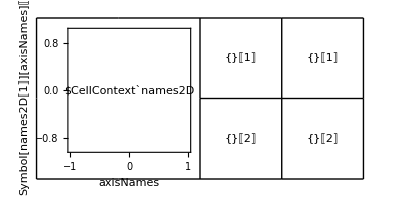

```mathematica
Block[{margin=2,dr,windows,blobPlt,blobsPlt,blobsDespecPlt},
dr=Table[ 
 Transpose[dataRange[Symbol[names2D[[i]]],"All"]+{{-margin,margin},{-margin,margin}}],
{i,3,Length[names2D]}];
windows=Flatten[{EdgeForm[Black],FaceForm[],Table[ 
 {Rectangle[Sequence@@(dr[[i]])],Text[ToString[i],{dr[[i,1,1]],dr[[i,2,2]]},{-1,-1}]},
{i,1,Length[dr]}]}];

blobPlt = Graphics[{windows,
Symbol[names2D[[1]]]["PlotData"]},Frame->True,PlotRange-> Symbol[names2D[[1]]]["PlotRange"],
FrameLabel->{{(Symbol[names2D[[1]]]["axisNames"])[[2]],""},{(Symbol[names2D[[1]]]["axisNames"])[[1]],Symbol[names2D[[1]]]["PlotLabel"]}}];

blobsPlt = Table[
Graphics[{
Symbol[names2D[[1]]]["PlotData"]},Frame->True,PlotRange-> Transpose[dr[[i-2]]],
FrameLabel->{{(Symbol[names2D[[i]]]["axisNames"])[[2]],""},{(Symbol[names2D[[i]]]["axisNames"])[[1]], ToString[i-2]}}],
{i,3,Length[names2D]}];

blobsDespecPlt = Table[
Graphics[{
Symbol[names2D[[i]]]["PlotData"]},Frame->True,PlotRange-> Transpose[dr[[i-2]]],
FrameLabel->{{(Symbol[names2D[[i]]]["axisNames"])[[2]],""},{(Symbol[names2D[[i]]]["axisNames"])[[1]], ToString[i-2]<>" Despeckled"}}],
{i,3,Length[names2D]}];

GraphicsGrid[{{blobPlt,SpanFromLeft,blobsPlt[[1]],blobsDespecPlt[[1]]},{SpanFromAbove,SpanFromBoth,blobsPlt[[2]],blobsDespecPlt[[2]]}},Frame->All]
]
```

### Surface plots

```mathematica
Block[{dr,hist,histoPlt,surfHistPlt},
dr=Round[dataRange[Symbol[names2D[[2]]],"All"]];
hist=HistoPlot3D[Symbol[names2D[[2]]],"LCaCb",N[1/1024],dr];
histoPlt=Graphics3D[hist,Lighting->"Neutral",Axes->True,AxesLabel->{"Ca","Cb","f"},BoxRatios->Flatten[{N[(dr[[All,2]]-dr[[All,1]])/Max[dr[[All,2]]-dr[[All,1]]]],1}]];
surfHistPlt=ListPlot3D[Transpose[Symbol[names2D[[2]]]["fBin"]],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,x,y}]],AxesLabel->{"Ca","Cb","f"},PlotRange->dr];
GraphicsRow[{histoPlt,surfHistPlt}]
]
```

## 7. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2D[[stage-4;;]]
names=names2D[[stage-4;;]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Do[Print["Getting : "<> names2D[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"];
Get[path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"],
{i,3,Length[names2D]}];
```

### Plot the Bin

```mathematica
Block[{margin=2,blobPlt,blobsPlt},
order={1,2};blobPlt=Graphics[{Flatten[{EdgeForm[Black],FaceForm[],Table[dr=Transpose[dataRange[Symbol[names2D[[i]]],"All"]+{{-margin,margin},{-margin,margin}}];{elipsePlt[Symbol[names2D[[i]]],2,order],Rectangle[Sequence@@(dr)],Text[StringTake[Symbol[names2D[[i]]]["PlotLabel"],-5],{dr[[1,1]],dr[[2,2]]},{-1,-1}]},
{i,3,Length[names2D]}]}],Symbol[names2D[[stage-5]]]["PlotData"]},Frame->True,PlotRange-> Symbol[names2D[[stage-5]]]["PlotRange"],FrameLabel->{{(Symbol[names2D[[stage-5]]]["axisNames"])[[2]],""},{(Symbol[names2D[[stage-5]]]["axisNames"])[[1]],Symbol[names2D[[stage-5]]]["PlotLabel"]}}];
blobsPlt=Table[
dr=dataRange[Symbol[names2D[[i]]],"All"]+{{-margin,margin},{-margin,margin}};
Graphics[{Symbol[names2D[[i]]]["PlotData"],elipsePlt[Symbol[names2D[[i]]],2,order]},Frame->True,PlotRange-> dr,FrameLabel->{{(Symbol[names2D[[i]]]["axisNames"])[[2]],""},{(Symbol[names2D[[i]]]["axisNames"])[[1]],StringTake[Symbol[names2D[[i]]]["PlotLabel"],-5]}}],
{i,3,Length[names2D]}];
GraphicsGrid[{{blobPlt,SpanFromLeft,blobsPlt[[1]]},{SpanFromAbove,SpanFromBoth,blobsPlt[[2]]}},Frame->All,ImageSize->1000]
]
```

```mathematica
Symbol[names2D[[3]]]["PlotLabel"]
```

## 8. Fit the Gaussian

```mathematica
blob=0;
name=names2D[[3+blob]]
```

### Check the Data

Set the important data to simple variable names.

```mathematica
μ={Symbol[name]["gMean"][[1]],Symbol[name]["gMean"][[2]]}
σ={Symbol[name]["gSigma"][[1]],Symbol[name]["gSigma"][[2]]}
θ=Symbol[name]["gTheta"]
```

Check that the axes max values are close to the mean

```mathematica
{CaMax,CbMax}=Position[Symbol[name]["fBin"],n_/;n==1.][[1]];
Row[{CaMax ,"==",μ[[1]]}]
Row[{CbMax,"==",μ[[2]]}]
```

### Density Plot

```mathematica
SetUpLCaCbColor[0];
```

```mathematica
{stat,redPlt,greenPlt,combPlt3DFun,combPltFun,overviewPlt}=gFitElems[Symbol[names2D[[3+blob]]],{1,2}];
```

```mathematica
Panel[Row[{DynamicModule[{incFit=True,incHisto=True,incStat=True},
Panel[Column[{
Framed[Panel[Row[{"Fit",Checkbox[Dynamic[incFit]],
"  Histo",Checkbox[Dynamic[incHisto]],
"  Stat",Checkbox[Dynamic[incStat]]}]]],
Panel[Dynamic[combPlt3D=combPlt3DFun[incFit,incHisto,incStat];Show[combPlt3D,ImageSize->500],Background->White]
]},Alignment->Center]]
],
DynamicModule[{incDen=True,incAxis=True,incElps=True,incTheta=True,incPhi=True,incStat=True},
Panel[Column[{
Framed[Panel[Row[{"Density",Checkbox[Dynamic[incDen]],
"  Axis",Checkbox[Dynamic[incAxis]],
"  Elipsis",Checkbox[Dynamic[incElps]],"  θ",Checkbox[Dynamic[incTheta]],"  ϕ",Checkbox[Dynamic[incPhi]],"  Stat",Checkbox[Dynamic[incStat]]}]]],
Panel[Dynamic[combPlt=combPltFun[incDen,incAxis,incElps,incTheta,incPhi,incStat];Show[combPlt,ImageSize->500]],Background->White]
},Alignment->Center]]
]
},Alignment->{Left,Top}],Style["Choose the elements to display",20],Alignment->{Left,Top}]
```

```mathematica
TabView[{TabView[{
Grid[{{stat},{
GraphicsGrid[{
{combPlt3D,         SpanFromLeft,combPlt,             SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All,ImageSize->1000]}}, Frame->All,Alignment->{Left,Center},Background->White],
GraphicsGrid[{
{combPlt3D,         SpanFromLeft,combPlt,              SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth},
{overviewPlt,     SpanFromLeft,   redPlt,                greenPlt}},Frame->All,ImageSize->1000]}],
TabView[{
GraphicsGrid[{
{combPlt3D,         SpanFromLeft,combPlt,             SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All,ImageSize->1000,Background->White],
GraphicsGrid[{
{combPlt3D,         SpanFromLeft,combPlt,              SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth},
{overviewPlt,     SpanFromLeft,redPlt,               greenPlt}},Frame->All,ImageSize->1000,Background->White]}],
TabView[{
GraphicsGrid[{
{combPlt,             SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All,ImageSize->1000,Background->White],
GraphicsGrid[{
{combPlt,             SpanFromLeft,SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromBoth},
{overviewPlt,    redPlt,              greenPlt}},Frame->All,ImageSize->1000,Background->White]}]
}]
```

```mathematica
x=Graphics[Circle[]];
GraphicsGrid[{{x,SpanFromLeft,x},{SpanFromAbove,SpanFromBoth,x},{SpanFromAbove,SpanFromBoth,x}},Frame->All]
GraphicsGrid[{{x,SpanFromLeft,SpanFromLeft},{SpanFromAbove,SpanFromBoth,SpanFromBoth},{x,x,x}},Frame->All]
GraphicsGrid[{
{x,                           SpanFromLeft,x                         , SpanFromLeft,x},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,x},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,x}},Frame->All]
```

```mathematica
Clear[mmAxis]
Block[{redPlt,greenPlt},
order={2,1};
redPlt=fitXPlt[Symbol[names2D[[3+blob]]],5,order];
greenPlt=fitYPlt[Symbol[names2D[[3+blob]]],5,order];

denPlt=ListDensityPlot[Symbol[names2D[[3+blob]]]["fBin"],AxesLabel->{"Cb","Ca"},InterpolationOrder->0];
denOpacityPlt=Graphics[Symbol[names2D[[3+blob]]]["PlotData"],Frame->True,PlotRange-> Symbol[names2D[[3+blob]]]["PlotRange"],FrameLabel->{{(Symbol[names2D[[3+blob]]]["axisNames"])[[2]],""},{(Symbol[names2D[[3+blob]]]["axisNames"])[[1]],Symbol[names2D[[3+blob]]]["PlotLabel"]}}];

axesPlt=Graphics[fit2DLinesPlt[Symbol[names2D[[3+blob]]],5,order]];

elpsPlt=Graphics[elipsePlt[Symbol[names2D[[3+blob]]],5,order]];

{thetaPlt,phiPlt}=fit2DAnglePlt[Symbol[names2D[[3+blob]]],order];

dr=dataRange[Symbol[names2D[[3+blob]]],5,order];
aspctRatio=(dr[[2,2]]-dr[[2,1]])/(dr[[1,2]]-dr[[1,1]]);
combPlt=Show[{denPlt,axesPlt,elpsPlt,
thetaPlt},PlotRange->dr,AspectRatio->aspctRatio,Frame->True,FrameLabel->{"Cb","Ca"}];
overviewPlt=Show[{denPlt,Graphics[{FaceForm[],EdgeForm[{Black,Opacity[1]}],Rectangle[{dr[[1,1]],dr[[2,1]]},{dr[[1,2]],dr[[2,2]]}]}]}];
If[aspctRatio≥1,
GraphicsGrid[{
{combPlt,SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All,ImageSize->1000],
GraphicsGrid[{
{combPlt,SpanFromLeft,SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromBoth},
{overviewPlt,redPlt,greenPlt}},Frame->All,ImageSize->1000]]
]
```

Proof that the eliptical plot is the same as the contor plot

```mathematica
μ={Symbol[name]["gMean"][[1]],Symbol[name]["gMean"][[2]]}
σ={Symbol[name]["gSigma"][[1]],Symbol[name]["gSigma"][[2]]}
θ=Symbol[name]["gTheta"]

sigTicks=Table[mmPts=MajorMinorAxesPoints[Reverse[μ],σ,Pi/2-θ,i];
GaussianFit[mmPts[[1,1,1]],mmPts[[1,1,2]],Reverse[μ],σ,Pi/2+θ],{i,1,5}];
contPlt=ContourPlot[GaussianFit[x,y,Reverse[μ],σ,Pi/2+θ],{x,dr[[1,1]],dr[[1,2]]},{y,dr[[2,1]],dr[[2,2]]},PlotRange->{dr[[1]],dr[[2]],{0,1}},Contours->sigTicks];

GraphicsRow[{Show[{contPlt,elipsePlt,axesPltPnts},Frame->True,FrameLabel->{"Cb","Ca"}],Show[{denPlt},Frame->True,FrameLabel->{"Cb","Ca"}]}]
```

### Surface plots

```mathematica
GaussianFit[Symbol[name],{1,2}]
```

```mathematica
dr=Round[dataRange[Symbol[name],"All"]];
hist=HistoPlot3D[Symbol[name],"LCaCb",N[1/1024],dr];
histoPlt=Graphics3D[hist,Lighting->"Neutral",Axes->True,AxesLabel->{"Ca","Cb","f"},BoxRatios->Flatten[{N[(dr[[All,2]]-dr[[All,1]])/Max[dr[[All,2]]-dr[[All,1]]]],1}]];
surfHistPlt=ListPlot3D[Transpose[Symbol[name]["fBin"]],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,x,y}]],AxesLabel->{"Ca","Cb","f"},PlotRange->dr];
fun=GaussianFit[Symbol[name],{1,2}];
fitPlt=Plot3D[fun[x,y],{x,dr[[1,1]],dr[[1,2]]},{y,dr[[2,1]],dr[[2,2]]},PlotRange->{dr[[1]],dr[[2]],{0,1}},PlotPoints->2 (dr[[1,2]]-dr[[1,1]]),PlotStyle->LCaCbColor[{0.7,μ[[1]]/255,μ[[2]]/255,0.6}],AxesLabel->{"Ca","Cb","f"}];
GraphicsRow[{Show[{histoPlt,fitPlt}],Show[{surfHistPlt,fitPlt}]}]
```

### Surface plots

```mathematica
ListPlot3D[Symbol[name]["fBin"],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,y,x}]],AxesLabel->{"Cb","Ca","f"}]
```

```mathematica
ListPlot3D[Symbol[name]["fBin"],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,y,x}]],PlotRange->{{μ[[2]]-10 σ[[1]],μ[[2]]+10 σ[[1]]},{μ[[1]]-10 σ[[2]],μ[[1]]+10 σ[[2]]},{0,1}},AxesLabel->{"Cb","Ca","f"}]
```

## 9. Combine the Plots Output

```mathematica
initColor=RGBColor[RandomReal[],RandomReal[],RandomReal[]];
Panel[DynamicModule[{color=initColor,opcty=1,out=Graphics3D[{Cuboid[{0,0,0},{255,255,255}]}],AxisLineThickness=Medium,EllipsLineThickness=Medium,sig={1,5},endSig=5,txtColor=initColor,txtOpacity=0,ellipsColor=initColor,ellipsOpacity=1,axisColor=initColor,axisOpacity=1,out2D=Graphics[{Rectangle[{0,0},{255,255}]}]},
Column[{
Row[{Panel[Column[{
Grid[{{Style["Axis",Bold],ColorSetter[Dynamic[color]],Slider[Dynamic[opcty],{0,1}]}}]
Button["Generate",Symbol[names2D[[3+blob]]]["fitPlot"]=.;
Symbol[names2D[[3+blob]]]["fitPlotColor"]=.;
Evaluate[Symbol[names2D[[3+blob]]]["fitPlotColor"]] = Directive[Opacity[opcty],color];
axisColor= color;ellipsColor= color;txtColor=color;
Evaluate[Symbol[names2D[[3+blob]]]["fitPlot"]]=fitComparisonPlt[Symbol[names2D[[3+blob]]],{1,2},Margin-> 5,ColorFunction->Function[{Ca,Cb,val},Directive[{Opacity[val/1.1],color}]] ];
out=Show[(Symbol[names2D[[3+blob]]]["fitPlot"])[[1]],(Symbol[names2D[[3+blob]]]["fitPlot"])[[2]]]
],
Panel[Dynamic[out],Background->White]
}]],
Panel[Column[{
Grid[{{Style["Axis",Bold],ColorSetter[Dynamic[axisColor]],Slider[Dynamic[axisOpacity],{0,1}]},
{Style["Ellips",Bold],ColorSetter[Dynamic[ellipsColor]],Slider[Dynamic[ellipsOpacity],{0,1}]},
{Style["Text",Bold],ColorSetter[Dynamic[txtColor]],Slider[Dynamic[txtOpacity],{0,1}]},
{Style["Sig",Bold],Dynamic[sig],IntervalSlider[Dynamic[sig],{1,10,1}]},
{Style["Ellipse Thick",Bold],Dynamic[EllipsLineThickness],Slider[Dynamic[EllipsLineThickness],{0,0.1}]},{Style["Axis Thick",Bold],Dynamic[AxisLineThickness],Slider[Dynamic[AxisLineThickness],{0,0.1}]}}],
Button["Generate",Symbol[names2D[[3+blob]]]["overlayElems"]=.;
Evaluate[Symbol[names2D[[3+blob]]]["overlayElems"]]=overlayElems[Symbol[names2D[[3+blob]]],order,AxisColor-> {Directive[Thickness[AxisLineThickness],Opacity[axisOpacity],axisColor],Directive[Opacity[axisOpacity],axisColor]}, TextColor->Directive[Opacity[txtOpacity],txtColor],MeanColor->Blue,PointSize-> 0.5,EllipsColor-> Directive[Thickness[EllipsLineThickness],Opacity[ellipsOpacity],ellipsColor],EllipsisSigma->sig];
out2D=Show[(Symbol[names2D[[3+blob]]]["overlayElems"])[[1]],(Symbol[names2D[[3+blob]]]["overlayElems"])[[2]]]
],
Panel[Dynamic[out2D],Background->White]
}]]}],
Button["Save",Save[path<>"Data"<>"/"<>matLabNames2D[[3+blob]]<>".m",Evaluate[names2D[[3+blob]]]]]
}]
]
]
```

```mathematica
names2D[[3+blob]]
```

```mathematica
DynamicModule[{AxisLineThickness=Medium,EllipsLineThickness=Medium,sig={1,5},endSig=5,txtColor=Symbol[names2D[[3+blob]]]["fitPlotColor"][[2]],txtOpacity=0,ellipsColor=Symbol[names2D[[3+blob]]]["fitPlotColor"][[2]],ellipsOpacity=1,axisColor=Symbol[names2D[[3+blob]]]["fitPlotColor"][[2]],axisOpacity=1,out=Graphics[{Rectangle[{0,0},{255,255}]}]},
Panel[Column[{
Grid[{{Style["Axis",Bold],ColorSetter[Dynamic[axisColor]],Slider[Dynamic[axisOpacity],{0,1}]},
{Style["Ellips",Bold],ColorSetter[Dynamic[ellipsColor]],Slider[Dynamic[ellipsOpacity],{0,1}]},
{Style["Text",Bold],ColorSetter[Dynamic[txtColor]],Slider[Dynamic[txtOpacity],{0,1}]},
{Style["Sig",Bold],Dynamic[sig],IntervalSlider[Dynamic[sig],{1,10,1}]},
{Style["Ellipse Thick",Bold],Dynamic[EllipsLineThickness],Slider[Dynamic[EllipsLineThickness],{0,0.1}]},{Style["Axis Thick",Bold],Dynamic[AxisLineThickness],Slider[Dynamic[AxisLineThickness],{0,0.1}]}}],
Button["Generate",Symbol[names2D[[3+blob]]]["overlayElems"]=.;
Evaluate[Symbol[names2D[[3+blob]]]["overlayElems"]]=overlayElems[Symbol[names2D[[3+blob]]],order,AxisColor-> {Directive[Thickness[AxisLineThickness],Opacity[axisOpacity],axisColor],Directive[Opacity[axisOpacity],axisColor]}, TextColor->Directive[Opacity[txtOpacity],txtColor],MeanColor->Blue,PointSize-> 0.5,EllipsColor-> Directive[Thickness[EllipsLineThickness],Opacity[ellipsOpacity],ellipsColor],EllipsisSigma->sig];
out=Show[(Symbol[names2D[[3+blob]]]["overlayElems"])[[1]],(Symbol[names2D[[3+blob]]]["overlayElems"])[[2]]]
],
Panel[Dynamic[out],Background->White],
Button["Save",Save[path<>"Data"<>"/"<>matLabNames2D[[3+blob]]<>".m",names2D[[3+blob]]]]
}]]
]
```

```mathematica
names2D[[3+blob]]
```

```mathematica
Show[{Symbol[names2D[[3+blob]]]["overlayElems"][[1,2]],Symbol[names2D[[3+blob]]]["overlayElems"][[1,1]]}]
```

```mathematica
{{axesPlt,elpsPlt,thetaPlt, phiPlt},combPltOpts}=overlayElems[bin,order];
combPlt=Function[{incDen,incAxis,incElps,incTheta,incPhi,incStat},Show[{If[incDen,denOpacityPlt],If[incAxis,axesPlt],If[incElps,elpsPlt],If[incTheta,thetaPlt],If[incPhi,phiPlt]}/.Null->Sequence[],If[incStat,Append[combPltOpts,Epilog-> Inset[stat,Extract[OptionValue[Graphics,combPltOpts,PlotRange],{{1,1},{2,2}}],{Left,Top}]],combPltOpts]]];
```

```mathematica
out
```

```mathematica
Symbol[names2D[[3+blob]]]["fitPlot"]
Show[(Symbol[names2D[[3+blob]]]["fitPlot"])[[1]],(Symbol[names2D[[3+blob]]]["fitPlot"])[[2]]]
```

```mathematica
Block[{},
{elems,opts}=fitComparisonPlt[Symbol[names2D[[3+blob]]],{1,2},Margin-> 5 ];
{elemsBlue,optsBlue}=fitComparisonPlt[BinSkinnedRotTopTailCaCbDespecblob2,{1,2},Margin-> 5,ColorFunction->Function[{Ca,Cb,val},Directive[{Opacity[val/1.1],RGBColor[0.0,0.1,1]}]] ];
GraphicsRow[{Show[elems,opts],
Show[elemsBlue,optsBlue]}]]
```

That RGB Image check thing.

```mathematica
img=-Graphics-;
```

```mathematica
imgData=Flatten[ImageData[img,"Byte"],1];
```

```mathematica
bins=ConstantArray[0,{256,256,256}];
```

```mathematica
Do[
bins[[ imgData[[i,1]]+1, imgData[[i,2]]+1, imgData[[i,3]]+1 ]]++;
,{i,1,Dimensions[imgData][[1]] }]
```

```mathematica
Dimensions[bins]
```

```mathematica
Max[Flatten[bins]]
```

```mathematica
Position[bins,n_/;n==5]
```

```mathematica
pos=Position[ImageData[img,"Byte"],n_/;n=={0,255,255}]
```

Are they all really {0,255,255}

```mathematica
Table[ImageData[img,"Byte"][[pos[[i,1]],pos[[i,2]]]],{i,1,Length[pos]}]
```

```mathematica
Count[bins,n_/;n>1,3]
```

```mathematica
Dimensions[ImageData[img,"Byte"]]
```

```mathematica
Show[{img,Graphics[{Table[Circle[pos[[i]],10],{i,1,Length[pos]}]}]}]
```

## That RGB Image check thing.

```mathematica
img=-Graphics-;
```

```mathematica
imgData=Flatten[ImageData[img,"Byte"],1];
```

```mathematica
bins=ConstantArray[0,{256,256,256}];
```

```mathematica
Do[
bins[[ imgData[[i,1]]+1, imgData[[i,2]]+1, imgData[[i,3]]+1 ]]++;
,{i,1,Dimensions[imgData][[1]] }]
```

```mathematica
Dimensions[bins]
```

```mathematica
Max[Flatten[bins]]
```

```mathematica
Position[bins,n_/;n==5]
```

```mathematica
pos=Position[ImageData[img,"Byte"],n_/;n=={0,255,255}]
```

Are they all really {0,255,255}

```mathematica
Table[ImageData[img,"Byte"][[pos[[i,1]],pos[[i,2]]]],{i,1,Length[pos]}]
```

```mathematica
Count[bins,n_/;n>1,3]
```

```mathematica
Dimensions[ImageData[img,"Byte"]]
```

```mathematica
Show[{img,Graphics[{Table[Circle[pos[[i]],10],{i,1,Length[pos]}]}]}]
```

The Combined Plots

## Init

```mathematica
blobNames={};
blobFiles = {};
blobGet = {};
blobs={};
blobsFiles={};
Do[setupFileSystem[ii,1,1];
Do[
AppendTo[blobNames,names2D[[i]]];
AppendTo[blobFiles,(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")];
AppendTo[blobGet,Button[names2D[[i]],If[MemberQ[blobs,nme],
Clear[nme];blobs=Complement[blobs,{nme}],
AppendTo[blobs,nme];AppendTo[ blobsFiles,fname];blobs=DeleteDuplicates[blobs];blobsFiles=DeleteDuplicates[blobsFiles];Get[fname]],Background->Dynamic[If[MemberQ[blobs,nme],Green,White]]]/.{nme->names2D[[i]],fname->(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")}];,
{i,3,Length[names2D]}];,{ii,1,5}]
```

Set : RGB     Subset :      Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/comb/mathematica/

3D | 2D
Bin.mat | Bin_Skinned_Rot_TopTail_CaCb.mat
Bin_Skinned.mat | Bin_Skinned_Rot_TopTail_CaCb_Despec.mat
Bin_Skinned_Rot.mat | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat
Bin_Skinned_Rot_TopTail.mat | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
Bin | Bin | Bin_Skinned_Rot_TopTail_CaCb | BinSkinnedRotTopTailCaCb
Bin_Skinned | BinSkinned | Bin_Skinned_Rot_TopTail_CaCb_Despec | BinSkinnedRotTopTailCaCbDespec
Bin_Skinned_Rot | BinSkinnedRot | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | BinSkinnedRotTopTailCaCbDespecblob2
Bin_Skinned_Rot_TopTail | BinSkinnedRotTopTail | Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | BinSkinnedRotTopTailCaCbDespecblob1

Set : RGB_GeneralSkin     Subset :      Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/

3D | 2D
RGB_GeneralSkin_Bin.mat | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb.mat
RGB_GeneralSkin_Bin_Skinned.mat | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec.mat
RGB_GeneralSkin_Bin_Skinned_Rot.mat | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat
RGB_GeneralSkin_Bin_Skinned_Rot_TopTail.mat | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
RGB_GeneralSkin_Bin | RGBGeneralSkinBin | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb | RGBGeneralSkinBinSkinnedRotTopTailCaCb
RGB_GeneralSkin_Bin_Skinned | RGBGeneralSkinBinSkinned | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec | RGBGeneralSkinBinSkinnedRotTopTailCaCbDespec
RGB_GeneralSkin_Bin_Skinned_Rot | RGBGeneralSkinBinSkinnedRot | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob2
RGB_GeneralSkin_Bin_Skinned_Rot_TopTail | RGBGeneralSkinBinSkinnedRotTopTail | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob1

Set : RGB_FSkin     Subset : Comb     Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/comb/mathematica/

3D | 2D
RGB_FSkin_Bin.mat | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb.mat
RGB_FSkin_Bin_Skinned.mat | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec.mat
RGB_FSkin_Bin_Skinned_Rot.mat | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat
RGB_FSkin_Bin_Skinned_Rot_TopTail.mat | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
RGB_FSkin_Bin | RGBFSkinBin | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb | RGBFSkinBinSkinnedRotTopTailCaCb
RGB_FSkin_Bin_Skinned | RGBFSkinBinSkinned | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec | RGBFSkinBinSkinnedRotTopTailCaCbDespec
RGB_FSkin_Bin_Skinned_Rot | RGBFSkinBinSkinnedRot | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | RGBFSkinBinSkinnedRotTopTailCaCbDespecblob2
RGB_FSkin_Bin_Skinned_Rot_TopTail | RGBFSkinBinSkinnedRotTopTail | RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | RGBFSkinBinSkinnedRotTopTailCaCbDespecblob1

Set : RGB_JSkin     Subset : Comb     Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/JSkin/comb/mathematica/

3D | 2D
RGB_JSkin_Bin.mat | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb.mat
RGB_JSkin_Bin_Skinned.mat | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec.mat
RGB_JSkin_Bin_Skinned_Rot.mat | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat
RGB_JSkin_Bin_Skinned_Rot_TopTail.mat | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
RGB_JSkin_Bin | RGBJSkinBin | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb | RGBJSkinBinSkinnedRotTopTailCaCb
RGB_JSkin_Bin_Skinned | RGBJSkinBinSkinned | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec | RGBJSkinBinSkinnedRotTopTailCaCbDespec
RGB_JSkin_Bin_Skinned_Rot | RGBJSkinBinSkinnedRot | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | RGBJSkinBinSkinnedRotTopTailCaCbDespecblob2
RGB_JSkin_Bin_Skinned_Rot_TopTail | RGBJSkinBinSkinnedRotTopTail | RGB_JSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | RGBJSkinBinSkinnedRotTopTailCaCbDespecblob1

Set : RGB_NSkin     Subset : Comb     Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/NSkin/comb/mathematica/

3D | 2D
RGB_NSkin_Bin.mat | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb.mat
RGB_NSkin_Bin_Skinned.mat | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec.mat
RGB_NSkin_Bin_Skinned_Rot.mat | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.mat
RGB_NSkin_Bin_Skinned_Rot_TopTail.mat | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.mat

3D MatLab | 3D Mathematica | 2D MatLab | 2D Mathematica
RGB_NSkin_Bin | RGBNSkinBin | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb | RGBNSkinBinSkinnedRotTopTailCaCb
RGB_NSkin_Bin_Skinned | RGBNSkinBinSkinned | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec | RGBNSkinBinSkinnedRotTopTailCaCbDespec
RGB_NSkin_Bin_Skinned_Rot | RGBNSkinBinSkinnedRot | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2 | RGBNSkinBinSkinnedRotTopTailCaCbDespecblob2
RGB_NSkin_Bin_Skinned_Rot_TopTail | RGBNSkinBinSkinnedRotTopTail | RGB_NSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1 | RGBNSkinBinSkinnedRotTopTailCaCbDespecblob1

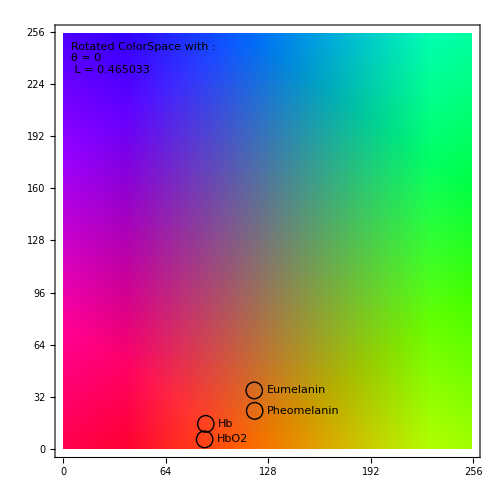
```mathematica
Clear[theoreticalValuesPlt];theoreticalValuesPlt=-Graphics-;
```

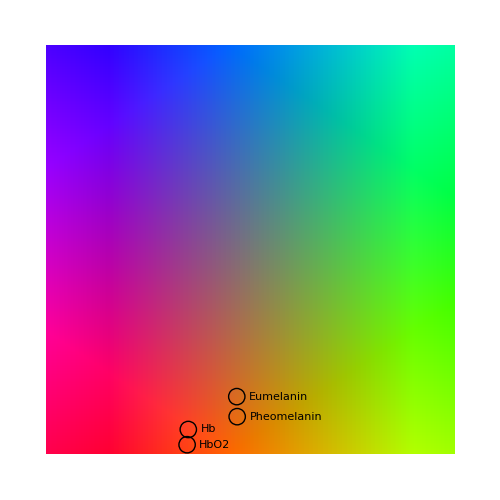
```mathematica
Clear[theoreticalValuesPltPlane];theoreticalValuesPltPlane=-Graphics-;
```

```mathematica
minCa=0;maxCa=255;
minCb=0;maxCb=255;
vtc={{0,0},{1,0},{1,1},{0,1}};
theoreticalValues3DPlt=Graphics3D[{Texture[theoreticalValuesPltPlane],Polygon[{{minCa,minCb,0},{maxCa,minCb,0},{maxCa,maxCb,0},{minCa,maxCb,0}},VertexTextureCoordinates->vtc]},Lighting->"Neutral"];
```

```mathematica
theoreticalValues3DPlt
```

-Graphics3D-

## Setup

```mathematica
Panel[Column[blobGet]]
```

BinSkinnedRotTopTailCaCbDespecblob2
BinSkinnedRotTopTailCaCbDespecblob1
RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob2
RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob1
RGBFSkinBinSkinnedRotTopTailCaCbDespecblob2
RGBFSkinBinSkinnedRotTopTailCaCbDespecblob1
RGBJSkinBinSkinnedRotTopTailCaCbDespecblob2
RGBJSkinBinSkinnedRotTopTailCaCbDespecblob1
RGBNSkinBinSkinnedRotTopTailCaCbDespecblob2
RGBNSkinBinSkinnedRotTopTailCaCbDespecblob1

```mathematica
blobFitPlotColor[i_]:=If[TrueQ[Head[Symbol[blobs[[i]]]["fitPlotColor"]]==Directive],Symbol[blobs[[i]]]["fitPlotColor"],White]
```

```mathematica
Panel[Row[{Panel[Column[Table[(Button["Move To Front #"<>ToString[i],blobs=BringToFront[blobs,{ii}];blobsFiles=BringToFront[blobsFiles,{ii}],Background->Dynamic[blobFitPlotColor[ii]]]//.ii->i),{i,1,Length[blobs]}]]],Dynamic[Panel[SwatchLegend[Table[blobFitPlotColor[i],{i,1,Length[blobs]}],Map[((StringSplit[Symbol[#]["PlotLabel"]," "])[[1]])&,blobs],LegendMarkers->"Bubble",LegendMarkerSize->16,LabelStyle->{GrayLevel[0.3],Bold,16}]]]}],"The Plot Order for the Sets"]
```

Move To Front #1
Move To Front #2
Move To Front #3
Move To Front #4
Move To Front #5The Plot Order for the Sets

```mathematica
figPath = $HomeDirectory <> "/Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter3/Figs/"
```

/Users/jaspershemilt/Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter3/Figs/

## Plots

```mathematica
outAllNextToEachOther3D = GraphicsRow[Table[Show[(Symbol[blobs[[i]]]["fitPlot"])[[1]],(Symbol[blobs[[i]]]["fitPlot"])[[2]],PlotLabel->Symbol[blobs[[i]]]["PlotLabel"] ],{i,1,Length[blobs]}],ImageSize->1000,Spacings->0];
Panel[Column[{Panel[outAllNextToEachOther3D
,Background->White,ImageSize->1000],
Button["Export",
Export[figPath<>"All_Next_To_Each_Other3D.jpg",outAllNextToEachOther3D,ImageResolution->300];
Export[figPath<>"All_Next_To_Each_Other3D.eps",outAllNextToEachOther3D];
Export[figPath<>"All_Next_To_Each_Other3D.pdf",outAllNextToEachOther3D]]}]]
```

-Graphics-
Export

```mathematica
margin=20;
rngs=Map[(OptionValue[Graphics3D,(Symbol[#]["fitPlot"])[[2]],PlotRange])&,blobs];
cmbRng={{Min[rngs[[All,1,1]]],Max[rngs[[All,1,2]]]}+{-margin,margin},{Min[rngs[[All,2,1]]],Max[rngs[[All,2,2]]]}+{-margin,margin},{Min[rngs[[All,3,1]]],Max[rngs[[All,3,2]]]} };

statTables=Map[Panel[Column[{Style[StringTake[Symbol[#]["PlotLabel"],{1,StringPosition[Symbol[#]["PlotLabel"]," ",1][[1,1]]}]
],Panel[statTable[Symbol[#],4,{1,2},Orientation-> "Vertical"],Background->White]}],Background->Symbol[#]["fitPlotColor"]]&,blobs];Panel[Column[{legend=SwatchLegend[Table[blobFitPlotColor[i],{i,1,Length[blobs]}],Map[((StringSplit[Symbol[#]["PlotLabel"]," "])[[1]])&,blobs],LegendMarkers->"Bubble",LegendMarkerSize->16,LabelStyle->{GrayLevel[0.3],Bold,16}];
outAllTogether3D = Grid[{{
Show[{theoreticalValues3DPlt,Map[((Symbol[#]["fitPlot"])[[1]])&,blobs]},PlotRange->cmbRng,Axes->True,AxesLabel->{"Ca","Cb",Column[{Style["Frequency",Bold],"f"},Alignment->Center]},ImageSize->1000,BoxRatios->{1,1,0.2},Epilog->Inset[legend,{Left,Top},{Left,Top}]]
,Column[{Sequence@@statTables}]}},Alignment->{Left,Top}];
Panel[outAllTogether3D ,Background->White],
Button["Export",
Export[figPath<>"All_Together_2D.jpg",outAllTogether2D,ImageResolution->300];
Export[figPath<>"All_Together_2D.eps",outAllTogether2D];
Export[figPath<>"All_Together_2D.pdf",outAllTogether2D]]}]]
```

-Graphics3D- | Bin 
θ | 0.9312 | 
μ | Ca | 108.5
 | Cb | 86.86
σ | Ca' | 6.256
 | Cb' | 2.7
FSkin 
θ | 1.094 | 
μ | Ca | 109.1
 | Cb | 85.9
σ | Ca' | 6.719
 | Cb' | 2.023
JSkin 
θ | 0.8294 | 
μ | Ca | 104.
 | Cb | 85.56
σ | Ca' | 6.985
 | Cb' | 3.056
NSkin 
θ | 1.006 | 
μ | Ca | 110.1
 | Cb | 87.64
σ | Ca' | 5.473
 | Cb' | 2.788
GeneralSkin 
θ | 1.442 | 
μ | Ca | 123.1
 | Cb | 106.5
σ | Ca' | 5.161
 | Cb' | 1.183
Export

```mathematica
blobsFiles[[2]]
blobs[[2]]
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/comb/mathematica/Data/RGB_FSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.m

RGBFSkinBinSkinnedRotTopTailCaCbDespecblob2

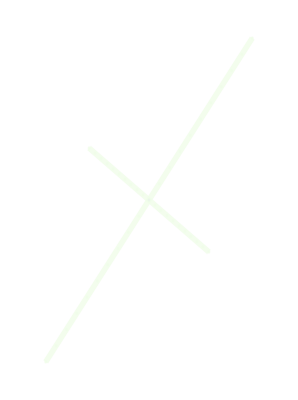
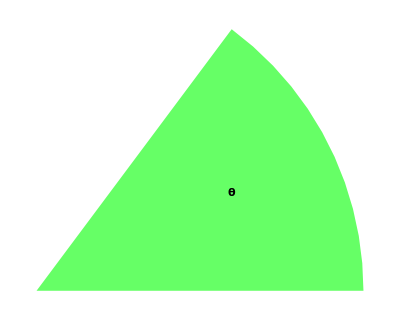
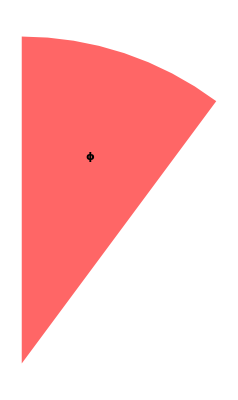
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{71.1923,145.881},{36.6617,137.052}},AspectRatio→1.34412,Frame→True,FrameLabel→{Ca,Cb}}}

```mathematica
Symbol[blobs[[1]]]["overlayElems"]
```

```mathematica
initColor
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
initColor=Map[(Symbol[#]["fitPlotColor"][[2]])&,blobs]
Panel[DynamicModule[{color=initColor,opcty=1,JSkinoutExport=Graphics3D[{Cuboid[{0,0,0},{255,255,255}]}],AxisLineThickness=4.0,EllipsLineThickness=4.0,sig={2,4},len=10,endSig=5,txtColor=initColor,txtOpacity=0,ellipsColor=initColor,ellipsOpacity=0.8,axisColor=initColor,axisOpacity=0.8,out2D=Graphics[{Rectangle[{0,0},{255,255}]}]},
Column[{
Row[{
Panel[Column[{
Grid[{
 {Style["Axis",  Bold],Table[ColorSetter[Dynamic[axisColor[[ii]]]]/.ii->i,{i,1,Length[axisColor]}],Slider[Dynamic[axisOpacity],{0,1}]},
{Style["Ellips",Bold],Table[ColorSetter[Dynamic[ellipsColor[[ii]]]]/.ii->i,{i,1,Length[ellipsColor]}] ,Slider[Dynamic[ellipsOpacity],{0,1}]},
{Style["Text",  Bold],Table[ColorSetter[Dynamic[txtColor[[ii]]]]/.ii->i,{i,1,Length[txtColor]}] ,Slider[Dynamic[txtOpacity],{0,1}]},
{Style["Sig",   Bold],Dynamic[sig],IntervalSlider[Dynamic[sig],{1,10,1}]},
{Style["len",   Bold],Dynamic[len],Slider[Dynamic[len],{1,10,1}]},
{Style["Ellipse Thick",Bold],Dynamic[EllipsLineThickness],Slider[Dynamic[EllipsLineThickness],{0,25}]},
{Style["Axis Thick",Bold],Dynamic[AxisLineThickness],Slider[Dynamic[AxisLineThickness],{0,25}]}}],
Button["Generate",Map[(Symbol[#]["overlayElems"]=.;)&,blobs];
Table[blob=blobs[[i]];
(Evaluate[Symbol[blob]["overlayElems"]]=overlayElems[Symbol[blob],{1,2},
AxisColor-> {Directive[AbsoluteThickness[AxisLineThickness],Opacity[axisOpacity],axisColor[[i]]],Directive[Opacity[axisOpacity],axisColor[[i]]]}, 
TextColor->Directive[Opacity[txtOpacity],txtColor[[i]]],
MeanColor->Blue,PointSize-> 0.5,
EllipsColor-> Directive[AbsoluteThickness[EllipsLineThickness],Opacity[ellipsOpacity],ellipsColor[[i]]],
EllipsisSigma->sig,AxisSigma->len]),{i,1,Length[blobs]}];
out2D=Show[Map[((Symbol[#]["overlayElems"])[[1,{1,2}]])&,blobs],(Symbol[blobs[[1]]]["overlayElems"])[[2]]]
],
Panel[Dynamic[out2D],Background->White]
}]]}],
Button["Save",Do[Save[blobsFiles[[i]],blobs[[i]]],{i,1,Length[blobs]}]]
}]
]
]
```

```mathematica
BinSkinnedRotTopTailCaCbDespecblob2["overlayElems"][[1,{1,2}]]/.RGBColor[_,_,_]->RGBColor[1,0,1]
```

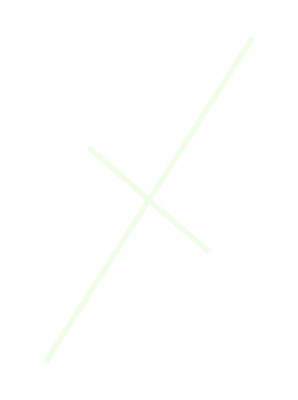
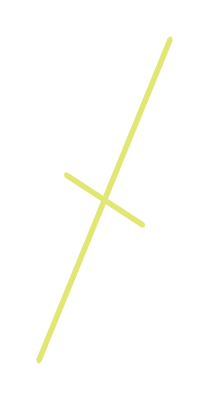
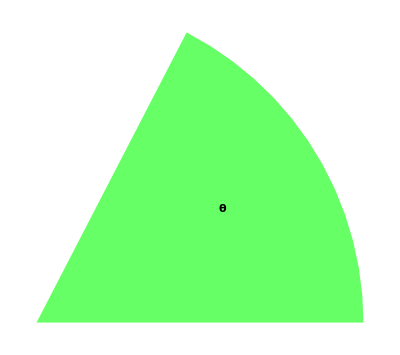
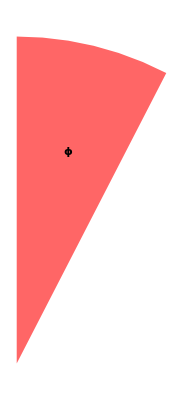
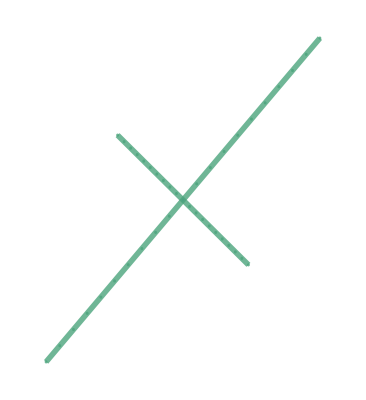
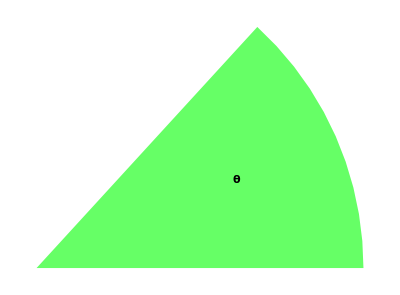
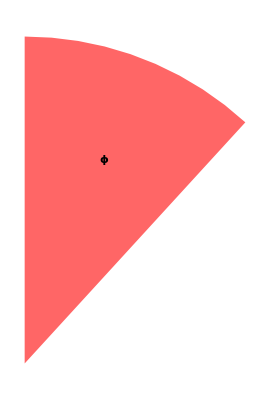
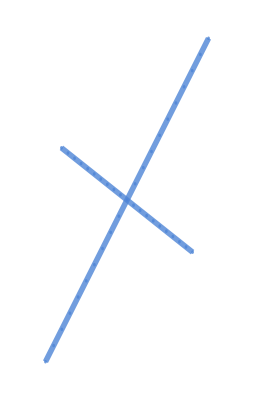
{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{71.1923,145.881},{36.6617,137.052}},AspectRatio→1.34412,Frame→True,FrameLabel→{Ca,Cb}}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{93.6351,124.483},{56.0499,115.742}},AspectRatio→1.93506,Frame→True,FrameLabel→{Ca,Cb}}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{56.7919,151.137},{34.0437,137.08}},AspectRatio→1.09212,Frame→True,FrameLabel→{Ca,Cb}}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{80.7705,139.347},{41.3968,133.877}},AspectRatio→1.5788,Frame→True,FrameLabel→{Ca,Cb}}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{117.189,128.918},{80.9446,132.127}},AspectRatio→4.36387,Frame→True,FrameLabel→{Ca,Cb}}}}

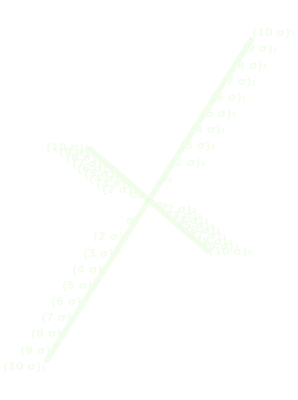
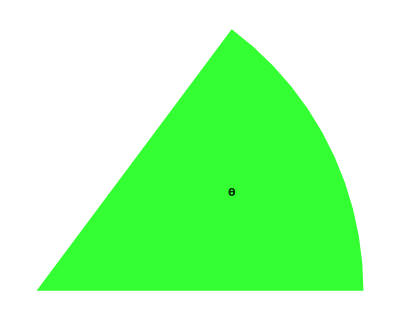
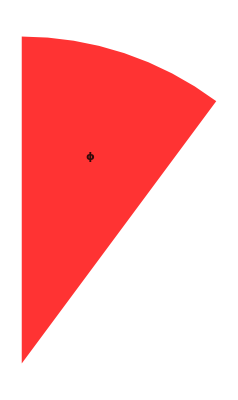
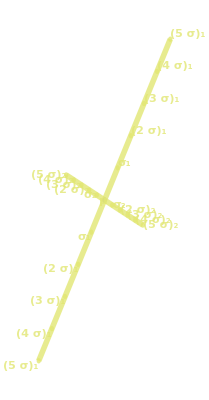
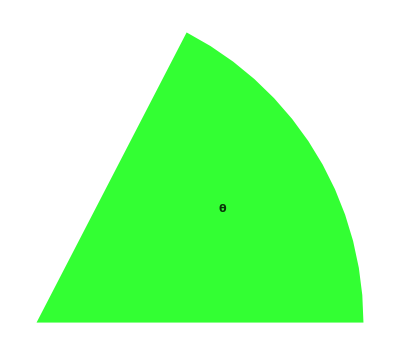
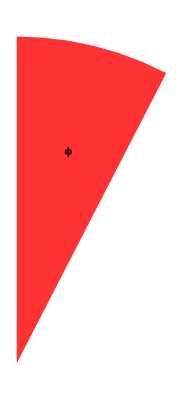
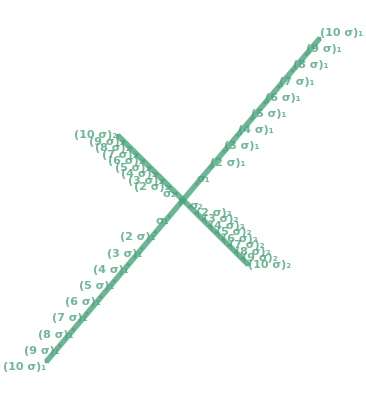
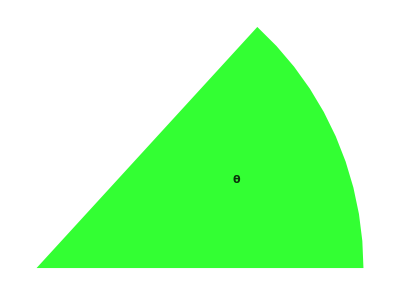
{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{71.1923,145.881},{36.6617,137.052}},AspectRatio→1.34412,Frame→True,FrameLabel→{Ca,Cb}}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{93.6351,124.483},{56.0499,115.742}},AspectRatio→1.93506,Frame→True,FrameLabel→{Ca,Cb}}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{56.7919,151.137},{34.0437,137.08}},AspectRatio→1.09212,Frame→True,FrameLabel→{Ca,Cb}}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{80.7705,139.347},{41.3968,133.877}},AspectRatio→1.5788,Frame→True,FrameLabel→{Ca,Cb}}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{PlotRange→{{117.189,128.918},{80.9446,132.127}},AspectRatio→4.36387,Frame→True,FrameLabel→{Ca,Cb}}}}

```mathematica
Map[(Symbol[#]["overlayElems"]=Symbol[#]["overlayElems"] /.{Thickness[_]->AbsoluteThickness[4]})&,blobs]
Map[(Symbol[#]["overlayElems"]=Symbol[#]["overlayElems"] /.{Opacity[_]->Opacity[0.8]})&,blobs]
```

```mathematica
statTables=Map[Panel[Column[{Style[StringTake[Symbol[#]["PlotLabel"],{1,StringPosition[Symbol[#]["PlotLabel"]," ",1][[1,1]]}]
],Panel[statTable[Symbol[#],4,{1,2},Orientation-> "Vertical"],Background->White]}],Background->Symbol[#]["fitPlotColor"]]&,blobs];Panel[Column[{legend=SwatchLegend[Table[blobFitPlotColor[i],{i,1,Length[blobs]}],Map[((StringSplit[Symbol[#]["PlotLabel"]," "])[[1]])&,blobs],LegendMarkers->"Bubble",LegendMarkerSize->16,LabelStyle->{GrayLevel[0.3],Bold,16}];
outAllTogether2D = Grid[{{Show[{theoreticalValuesPlt,Graphics[{Circle[{128,128},1]}],Map[({Symbol[#]["overlayElems"][[1,2]],Symbol[#]["overlayElems"][[1,1]]} /.RGBColor[_,_,_]->RGBColor[1,1,1])&,Reverse[blobs]],Map[({Symbol[#]["overlayElems"][[1,2]],Symbol[#]["overlayElems"][[1,1]]} )&,Reverse[blobs]]},ImageSize->700,Axes->True,AxesLabel->{"Ca","Cb"},Epilog->Inset[legend,{250,250},{Right,Top}]],Column[{Sequence@@statTables}]}},Alignment->{Left,Center}];
Panel[outAllTogether2D ,Background->White],
Button["Export",
Export[figPath<>"All_Together_2D.jpg",outAllTogether2D,ImageResolution->300];
Export[figPath<>"All_Together_2D.eps",outAllTogether2D];
Export[figPath<>"All_Together_2D.pdf",outAllTogether2D]]}]]
```

-Graphics- | Bin 
θ | 0.9312 | 
μ | Ca | 108.5
 | Cb | 86.86
σ | Ca' | 6.256
 | Cb' | 2.7
FSkin 
θ | 1.094 | 
μ | Ca | 109.1
 | Cb | 85.9
σ | Ca' | 6.719
 | Cb' | 2.023
JSkin 
θ | 0.8294 | 
μ | Ca | 104.
 | Cb | 85.56
σ | Ca' | 6.985
 | Cb' | 3.056
NSkin 
θ | 1.006 | 
μ | Ca | 110.1
 | Cb | 87.64
σ | Ca' | 5.473
 | Cb' | 2.788
GeneralSkin 
θ | 1.442 | 
μ | Ca | 123.1
 | Cb | 106.5
σ | Ca' | 5.161
 | Cb' | 1.183
Export

```mathematica
statTables=Map[Panel[Column[{Style[StringReplace[Symbol[#]["PlotLabel"],{"Blob1"->"","Blob2"->""}]],Panel[statTable[Symbol[#],4,{1,2}],Background->White]}],Background->Symbol[#]["fitPlotColor"]]&,blobs]
```

{Bin CaCb Bin 
 | θ | μ | σ
Ca' | 0.9312 | 108.5 | 6.256
Cb' |  | 86.86 | 2.7,FSkin CaCb Bin 
 | θ | μ | σ
Ca' | 1.094 | 109.1 | 6.719
Cb' |  | 85.9 | 2.023,JSkin CaCb Bin 
 | θ | μ | σ
Ca' | 0.8294 | 104. | 6.985
Cb' |  | 85.56 | 3.056,NSkin CaCb Bin 
 | θ | μ | σ
Ca' | 1.006 | 110.1 | 5.473
Cb' |  | 87.64 | 2.788,GeneralSkin CaCb Bin 
 | θ | μ | σ
Ca' | 1.442 | 123.1 | 5.161
Cb' |  | 106.5 | 1.183}

#### Save the color Definitions

```mathematica
Map[(CellPrint[Cell[BoxData[RowBox[{(StringReplace[(StringSplit[Symbol[#]["PlotLabel"]," "])[[1]],"&"->""])<>"InitColor","=",ToBoxes[(Symbol[#]["fitPlotColor"])[[2]],StandardForm],";"}]],"Code",InitializationCell->True]])&,blobs]
```

```mathematica
FJNInitColor=-Graphics-;
```

```mathematica
FSkinInitColor=-Graphics-;
```

```mathematica
GeneralSkinInitColor=-Graphics-;
```

```mathematica
JSkinInitColor=-Graphics-;
```

```mathematica
NSkinInitColor=-Graphics-;
```

## WhiteOut and Blackout

#### Init

```mathematica
Clear[rgbCubeInLCaCb]
rgbCubeInLCaCb[scale_:1,θ_:0]:=Translate[GeometricTransformation[Rotate[Rotate[Rotate[{EdgeForm[Black],FaceForm[],Cuboid[{0,0,0},{scale,scale,scale}]},Pi/4,{0,1,0}],-ArcTan[1/Sqrt[2]],{0,0,1}],θ,{1,0,0}],ScalingMatrix[{1/(√3),√(3/8),1/(√2)}]],{0,0.5 scale,0.5 scale}];

Graphics3D[{Opacity[0.2],rgbCubeInLCaCb[1]},ViewVertical->{1, 0, 0},Axes->True,AxesLabel->{"L","Ca","Cb"}]
```

-Graphics3D-

```mathematica
Clear[val]
Block[{θ,R},
θ=0;
R=Simplify[RotationMatrix[θ,{1,0,0}]. RotationMatrix[-ArcTan[1/Sqrt[2]],{0,0,1}]. RotationMatrix[Pi/4,{0,1,0}]];

toLCaCb=Function[{val},((rrR . val) {1/(√3),√(3/8),1/(√2)})+{0,0.5,0.5}]/.{rrR-> Simplify[RotationMatrix[θ,{1,0,0}]. RotationMatrix[-ArcTan[1/Sqrt[2]],{0,0,1}]. RotationMatrix[Pi/4,{0,1,0}]]};
fromLCaCb=Function[{val},iR . ((val -{0,0.5,0.5}) {√3,2 √(2/3),√2}) ]/.{iR->Inverse[R]};
]
```

```mathematica
Clear[WOBOPathLCaCb]
WOBOPathLCaCb[rgb:{_,_,_}]:=Module[{color,ordering,sc},
sc=N[1/128];
color=RGBColor[rgb];
ordering = Ordering[rgb];
{a,b,c}=Part[rgb,ordering];
{
toLCaCb[{0,0,0}],
toLCaCb[ReplacePart[rgb-b,{ordering[[1]]->0,ordering[[2]]->0}]],
toLCaCb[(rgb-a)],
toLCaCb[(rgb+(1-c))],
toLCaCb[(ReplacePart[rgb+(1-b),{ordering[[3]]->1,ordering[[2]]->1}])],
toLCaCb[({1,1,1})]}
]
```

```mathematica
WOBOTubePathLCaCb[rgb:{_,_,_}]:=Module[{color,ordering,sc},
sc=N[1/128];
color=RGBColor[rgb];
ordering = Ordering[rgb];
{a,b,c}=Part[rgb,ordering];
{FaceForm[color,color],EdgeForm[],
Tube[ WOBOPathLCaCb[rgb]
,sc]
}]
```

```mathematica
WOBOPath[rgb:{_,_,_}]:=Module[{color,ordering},
color=RGBColor[rgb];
ordering = Ordering[rgb];
{a,b,c}=Part[rgb,ordering];
{
{0,0,0},
ReplacePart[rgb-b,{ordering[[1]]->0,ordering[[2]]->0}],
rgb-a,
rgb+(1-c),
ReplacePart[rgb+(1-b),{ordering[[3]]->1,ordering[[2]]->1}],
{1,1,1}
}]
```

```mathematica
colorPath[path_,disc_:N[1/256]]:=Module[{},
Table[
vec=path[[j+1]]-path[[j]];
 dist=Max[vec];
Table[
RGBColor[path[[j]]+i  vec/dist],{i,0,dist,disc}]
,{j,1,Length[path]-1}]
]
```

```mathematica
normColor[RGBColor[{r_,g_,b_}],bright_:0.5]:=Module[{lum},lum=3 bright ;
brighten=(lum-r-g-b)/3;
RGBColor[r+brighten,g+ brighten,b+ brighten]
]
```

```mathematica
Clear[WOBOColorEffect]
Options[WOBOColorEffect]=Flatten[{TickNames->{"Black","λ_B^Sat","λ_B","λ_W","λ_W^Sat","White"},Normed->True,TextInGraphic->False,Options[Graphics]}];
WOBOColorEffect[rgb_List,opts:OptionsPattern[]]:=Module[{ticks,ht,hta,path,clrPath,normClrPath,lens,starts,aspect,strip,txtShift,txtAlign},
ticks=OptionValue[TickNames];(*{"Black","λ_B^Sat","λ_B","λ_W","λ_W^Sat","White"};*)
aspect=1/7;
path=WOBOPath[rgb];
clrPath=colorPath[path];
normClrPath=Map[normColor,clrPath,{2} ];
lens=Map[Length,normClrPath];
starts=Table[Total[lens[[1;;i]]],{i,0,Length[lens]}];
ht=aspect starts[[-1]];
hta=aspect starts[[-1]]/6;
If[TrueQ[OptionValue[TextInGraphic]],txtShift=2;txtAlign={Center,Center},txtShift=1;txtAlign={Left,Center}];
If[OptionValue[Normed],
strip={Table[{Table[{normClrPath[[j,i]],Rectangle[{i+starts[[j]],0},{i+starts[[j]]+1,ht}]},{i,1,Length[normClrPath[[j]]]}]},{j,1,Length[normClrPath]}],Text["Brightness Adjusted Color",{(hta+starts[[-1]])/txtShift, ht/2},txtAlign]},
strip={Table[{Table[{clrPath[[j,i]],Rectangle[{i+starts[[j]],0},{i+starts[[j]]+1,ht}]},{i,1,Length[clrPath[[j]]]}]},{j,1,Length[clrPath]}],Text["Detected Color"  ,{(hta+starts[[-1]])/txtShift,ht/2},txtAlign]},
strip ={Table[{Table[{
normClrPath[[j,i]],Rectangle[{i+starts[[j]],ht/2+hta/2 },{i+starts[[j]]+1,ht    }],
clrPath[[j,i]],         Rectangle[{i+starts[[j]],0        },{i+starts[[j]]+1,ht/2-hta/2}]},{i,1,Length[normClrPath[[j]]]}]},{j,1,Length[normClrPath]}],
Text["Detected Color"  ,{(hta+starts[[-1]])/txtShift,ht/4},txtAlign],Text["Brightness Adjusted Color",{(hta+starts[[-1]])/txtShift,3 ht/4},txtAlign]}
];
Graphics[{
Table[{Black,Rectangle[{1+starts[[j]],-5},{2+starts[[j]],ht+hta}],Text[ticks[[j]],{1+starts[[j]],ht+hta},{Center,Bottom}]},{j,{1,3,4,6}}],
Table[{Black,Rectangle[{1+starts[[j]],-5},{2+starts[[j]],ht+hta}],Text[ticks[[j]],{1+starts[[j]],-hta},{Center,Top}]},{j,{2,5}}],,
strip},FilterRules[{opts},Options[Graphics]]]
]
```

#### WOBO Plots

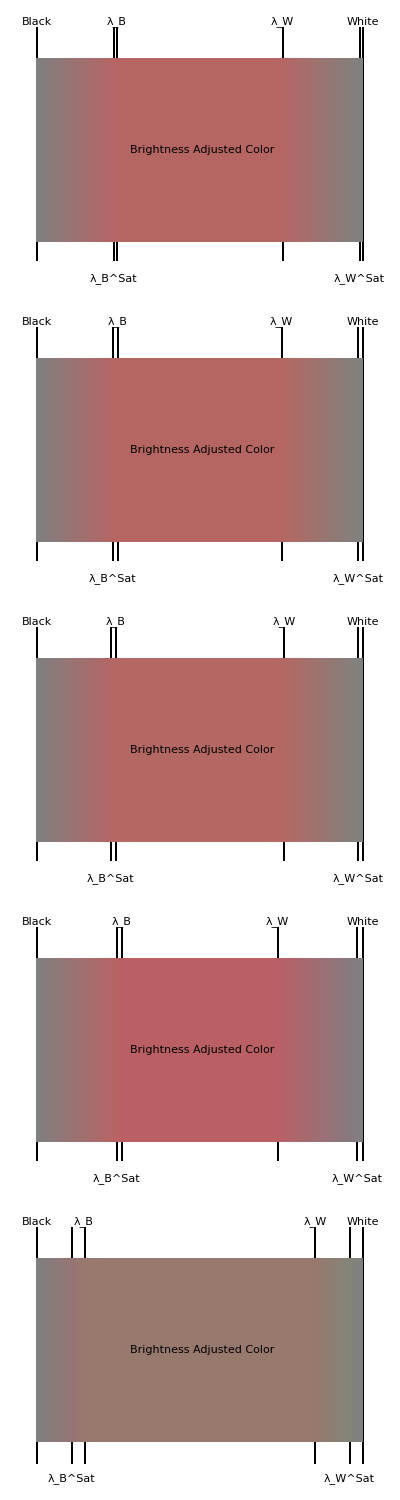
-Graphics3D- | -Graphics-

```mathematica
lines=Table[
μ=Symbol[blobs[[blob]]]["gMean"]/256;
σ=Symbol[blobs[[blob]]]["gSigma"]/256;
θ=Symbol[blobs[[blob]]]["gTheta"];
Table[val=GaussianFitFun[Ca,Cb,μ,σ,θ];{Opacity[val],If[val>0.05,WOBOTubePathLCaCb[fromLCaCb[{0.5,Ca,Cb}]],Sequence[]]},
{Ca,μ[[1]]-3 σ[[1]],μ[[1]]+3 σ[[1]],1/128},{Cb,μ[[2]]-3 σ[[2]],μ[[2]]+3 σ[[2]],1/128}],
{blob,1,Length[blobs]}];

colors=Table[
μ=Symbol[blobs[[blob]]]["gMean"]/256;
σ=Symbol[blobs[[blob]]]["gSigma"]/256;
θ=Symbol[blobs[[blob]]]["gTheta"];
colors=WOBOColorEffect[fromLCaCb[{0.5,μ[[1]],μ[[2]]}],ImageSize->350,Normed->True,TextInGraphic->True],
{blob,1,Length[blobs]}];
cube=Graphics3D[{rgbCubeInLCaCb[],lines},ViewVertical->{1,0,0},Axes->True,AxesLabel->{"L","Ca","Cb"},Lighting->{{"Ambient",White}},ImageSize->500];
Grid[{{cube,Column[colors]}},Alignment->Left]
```

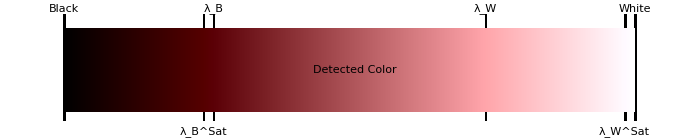
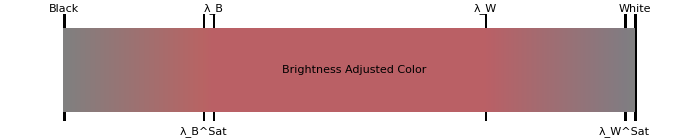
-Graphics- |  |  |  | 
JSkin 
θ | 0.8294 | 
μ | Ca | 104.
 | Cb | 85.56
σ | Ca' | 6.985
 | Cb' | 3.056
 | 0-1 | 0-255
Black | 0. | 0
λ_B^Sat | 0.111 | 28
λ_B | 0.125 | 32
λ_W | 0.772 | 197
λ_W^Sat | 0.993 | 253
White | 1. | 255 | -Graphics3D- |  |  | 
 |  |  |  | 
 |  |  |  | 
-Graphics- |  |  |  |

```mathematica
blob=3;
μ=Symbol[blobs[[blob]]]["gMean"]/256;
σ=Symbol[blobs[[blob]]]["gSigma"]/256;
θ=Symbol[blobs[[blob]]]["gTheta"];
stat=Panel[Column[{Style[StringTake[Symbol[blobs[[blob]]]["PlotLabel"],{1,StringPosition[Symbol[blobs[[blob]]]["PlotLabel"]," ",1][[1,1]]}]],Panel[statTable[Symbol[blobs[[blob]]],4,{1,2},Orientation-> "Vertical"],Background->White],Panel[Grid[Transpose[{{"","Black","λ_B^Sat","λ_B","λ_W","λ_W^Sat","White"},Flatten[{"0-1",Map[(NumberForm[#,3])&,N[(WOBOPathLCaCb[fromLCaCb[{0.5,μ[[1]],μ[[2]]}]])][[All,1]]]}],Flatten[{"0-255",Round[N[255(WOBOPathLCaCb[fromLCaCb[{0.5,μ[[1]],μ[[2]]}]])][[All,1]]]}]}], Frame->All,Alignment->{Center,Center}],Background->White]}],Background->Lighter[(Symbol[blobs[[blob]]]["fitPlotColor"])[[2]],0.7]];
lines=Table[val=GaussianFitFun[Ca,Cb,μ,σ,θ];{Opacity[val],If[val>0.05,WOBOTubePathLCaCb[fromLCaCb[{0.5,Ca,Cb}]],Sequence[]]},
{Ca,μ[[1]]-2 σ[[1]],μ[[1]]+3 σ[[1]],1/128},{Cb,μ[[2]]-2 σ[[2]],μ[[2]]+3 σ[[2]],1/128}];
cube=Graphics3D[{rgbCubeInLCaCb[],lines},ViewVertical->{1,0,0},Axes->True,AxesLabel->{"L","Ca","Cb"},ImageSize->500,Lighting->{{"Ambient",White}},ViewPoint->{1.3,3.9,2}];
colorsNorm  =WOBOColorEffect[fromLCaCb[{0.5,μ[[1]],μ[[2]]}],ImageSize->700,Normed->True,TextInGraphic->True];
colorsDtctd=WOBOColorEffect[fromLCaCb[{0.5,μ[[1]],μ[[2]]}],ImageSize->700,Normed->False,TextInGraphic->True];
colors=WOBOColorEffect[fromLCaCb[{0.5,μ[[1]],μ[[2]]}],ImageSize->700,Normed->"Both"];
Panel[Grid[{
{colorsDtctd,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},
{stat,Panel[cube,Background->White],SpanFromLeft,SpanFromLeft,SpanFromLeft},
{SpanFromAbove,SpanFromAbove,SpanFromBoth,SpanFromBoth,SpanFromBoth},
{SpanFromAbove,SpanFromAbove,SpanFromBoth,SpanFromBoth,SpanFromBoth},
{colorsNorm,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft}
},Alignment->{Left,Top}],FrameMargins->5]
```

#### WhitePoint Plots

```mathematica
Graphics3D[{rgbCubeInLCaCb[1],Table[WOBOTubePathLCaCb[ReplacePart[toLCaCb[{RandomReal[],RandomReal[],RandomReal[]}],1->0.5]],{i,1,200}]},ViewVertical->{1,0,0},Axes->True]
```

-Graphics3D-

Generate a new sample set with 24 colors. Generate the pallets then display and photograph to generate the new set.

```mathematica
WOBOpath=WOBOpathBase<>"WhitePoint/"<>FromCharacterCode[Table[RandomInteger[Flatten[{ToCharacterCode["A"],ToCharacterCode["Z"]}]],{i,1,10}]]<>"/"
Quiet[CreateDirectory[WOBOpath],CreateDirectory::filex]
Quiet[CreateDirectory[WOBOpath<>"src/"],CreateDirectory::filex]
Quiet[CreateDirectory[WOBOpath<>"figs/"],CreateDirectory::filex]
startColors=Table[{RandomReal[{0,0.95}],RandomReal[{0,0.95}],RandomReal[{0,0.95}]},{i,1,24}];
Save[WOBOpath<>"startColors.m",startColors];
paths=Map[WOBOPath,startColors][[All,{3,4}]];
colors=Map[((colorPath[#,N[1/256]])[[1]])&,paths];
selLen=Min[{Min[Map[Length,colors]],42}]
selection=Map[RandomSample[#,selLen]&,colors];
panels=Table[GraphicsGrid[ArrayReshape[Map[(Graphics[{#,Rectangle[]}])&,selection[[All,i]] ],{4,6}],ImageSize->Full],{i,1,selLen}];
theoryColors=Graphics3D[{rgbCubeInLCaCb[1],Table[WOBOTubePathLCaCb[startColors[[i]]]/.{Tube[{_,_,a_,b_,_,_},r_]:> Tube[{a,b},r]},{i,1,Length[startColors]}]},ViewVertical->{1,0,0},Axes->True];
Do[
Export[WOBOpath<>"src/Panel"<>ToString[i]<>".jpg",panels[[i]],ImageResolution->300];
,{i,1,selLen}]
Export[WOBOpath<>"figs/TheoreticalDisrto.jpg",theoryColors,ImageResolution->300 ]
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/WhitePoint/WhitePoint/GXBGIFUFMH/

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/WhitePoint/WhitePoint/GXBGIFUFMH/

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/WhitePoint/WhitePoint/GXBGIFUFMH/src/

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/WhitePoint/WhitePoint/GXBGIFUFMH/figs/

42

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/WhitePoint/WhitePoint/GXBGIFUFMH/figs/TheoreticalDisrto.jpg

```mathematica
theoryColors
```

-Graphics3D-

```mathematica
Graphics3D[{Black,Cuboid[{0,0,0},{1,1,1}],Table[WOBOPath[{RandomReal[],RandomReal[],RandomReal[]}],{i,1,200}]},ViewVertical->{1,1,1}]
```

-Graphics3D-

```mathematica
R=Simplify[RotationMatrix[Pi/4,{1,0,0}]. RotationMatrix[-ArcTan[1/Sqrt[2]],{0,0,1}]. RotationMatrix[0,{0,1,0}]]
```

{{1/(√3),1/(√3),1/(√3)},{1/6 (3-√3),1/(√3),1/6 (-3-√3)},{1/6 (-3-√3),1/(√3),1/6 (3-√3)}}

```mathematica
cube=Flatten[{EdgeForm[Black],FaceForm[],Cuboid[{0,0,0},{1,1,1}],Table[WOBOPath[{RandomReal[],RandomReal[],RandomReal[]}],{i,1,200}]}];
cubeRot=Normal@Rotate[Rotate[Rotate[cube,Pi/4,{0,1,0}],-ArcTan[1/Sqrt[2]],{0,0,1}],Pi/4,{1,0,0}];
```

```mathematica
Graphics3D[cubeRot,ViewVertical->{1, 0, 0},Axes->True]
```

-Graphics3D-

```mathematica
Graphics3D[GeometricTransformation[cubeRot,ScalingMatrix[{1/(√3),√(3/8),1/(√2)}]],AspectRatio->1]
```

-Graphics3D-